```mathematica
Quit[]
```

#### Kernels Control

```mathematica
LaunchKernels[8]
```

{KernelObject(1,local),KernelObject(2,local),KernelObject(3,local),KernelObject(4,local),KernelObject(5,local),KernelObject(6,local),KernelObject(7,local),KernelObject(8,local)}

```mathematica
CloseKernels[Kernels[]]
```

```mathematica
Kernels[]
```

### Main

#### Declaration

```mathematica
ParallelEvaluate[Off[General::stop]];
```

```mathematica
ParallelEvaluate[On[General::stop]];
```

```mathematica
If[$OperatingSystem=="Windows",{dir="D:/Documents/2-d-data";},{dir="/home/huangys/mount/DATA/Documents/2-d-data";}];
```

```mathematica
Kernel[x_?NumberQ]:=NIntegrate[ϕ3[p]/(p-x)^2,{p,0,1}]
```

```mathematica
A[ω_][ϕ1_,ϕ2_,ϕ3_]:=(1-ℂ)(1/(1-ω)NIntegrate[ϕ1[x]ϕ2[x/ω] ϕ3[p]/(p-(x-ω)/(1-ω))^2,{p,0,1},{x,0,ω},AccuracyGoal->12,Method->"GlobalAdaptive"]-1/ω NIntegrate[ϕ1[x]ϕ3[(x-ω)/(1-ω)] ϕ2[p]/(p-x/ω)^2,{p,0,1},{x,ω,1},AccuracyGoal->12,Method->"GlobalAdaptive"]+1/Nc 1/(1-ω)NIntegrate[ϕ3[x],{x,0,1}]NIntegrate[ϕ1[x]ϕ2[x/ω],{x,0,ω},AccuracyGoal->12,Method->"GlobalAdaptive"])(*r1=1*)
```

```mathematica
Clear[m1,m2,β,Nx]; (*β=1 unit*)
Nx=500;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=g^2/(2Pi)Nc*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
```

```mathematica
Nc=1000;ℂ=0;(*ℂ denotes the interchange of final states.*)
```

```mathematica
vMatx[n_,m_]:=(vMatx[n-1,m-1] m/(m-1)+(8m)/(n+m-1)((1+(-1)^(n+m))/2))
vMatx[1,m_]:=4(1+(-1)^(m+1));
vMatx[n_,1]:=4/n(1+(-1)^(n+1));
```

```mathematica
Determineϕx[m1_,m2_,β_,Nx_]:=
Module[{HMatx,VMatx,vals,vecs,g,ϕx,ϕ},
SetSharedVariable[vecs,m1,m2,β,g];
SetSharedFunction[g];
HMatx=ParallelTable[4Min[n,m]((-1)^(n+m)(m1^2-β^2)+(m2^2-β^2)),{n,1,Nx},{m,1,Nx}];
VMatx=ParallelTable[vMatx[n,m],{n,1,Nx},{m,1,Nx}];
{vals,vecs}=Eigensystem[N[HMatx+VMatx]];
Do[g[j]=Dot[ParallelTable[Sin[i ArcCos[2x-1]],{i,1,Nx}],vecs[[j]]],{j,1,Nx}];
ϕx=ParallelTable[Quiet[g[Nx-n]/√NIntegrate[g[Nx-n]^2,{x,0,1}]],{n,0,20}];
Clear[g];
{√Reverse[vals] β,ϕx}
]
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
```

```mathematica
Mn[n_][vals_]:=vals[[n+1]];
```

```mathematica
ω[M1_,M2_,M3_]:=(*-*)(√((M1^2+M2^2-M3^2)^2-4 M1^2 M2^2))/(2 M1^2)+M2^2/(2 M1^2)-M3^2/(2 M1^2)+1/2
```

```mathematica
ASin[n_][m1_]:=
Module[{ϕx,m2,ϕ,Vals,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,ωnow,filename},
(*SetSharedVariable[m2,m1];*)
m2=m1;
filename="/eigenstate_m-"<>ToString[m1]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Vals,ϕx}=Determineϕx[m1,m2,β,Nx];
ϕ[x_]=ϕx;
Export[dir<>filename,{Vals,ϕx},"TSV"]
},
{
{Vals,ϕx}=Import[dir<>filename,"TSV"];
ϕ[x_]=ϕx;
}
];
{M1,ϕ1}={Mn[#][Vals],ϕn[#][ϕ]}&[n];{M2,ϕ2}={Mn[#][Vals],ϕn[#][ϕ]}&[1];{M3,ϕ3}={Mn[#][Vals],ϕn[#][ϕ]}&[1];
Print[ω[M1,M2,M3]];
Ares=A[ω[M1,M2,M3]][ϕ1,ϕ2,ϕ3];
Print[{m1^2,Ares}];
{m1^2,Ares}
]
```

```mathematica
At[n_][ma_,mb_,δm_]:=Table[
Module[{ϕx,m2,ϕ,Vals,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,ωnow,filename},
(*SetSharedVariable[m2,m1];*)
m2=m1;
filename="/eigenstate_m-"<>ToString[m1]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Vals,ϕx}=Determineϕx[m1,m2,β,Nx];
ϕ[x_]=ϕx;
Export[dir<>filename,{Vals,ϕx},"TSV"]
},
{
{Vals,ϕx}=Import[dir<>filename,"TSV"];
ϕ[x_]=ϕx;
}
];
{M1,ϕ1}={Mn[#][Vals],ϕn[#][ϕ]}&[n];{M2,ϕ2}={Mn[#][Vals],ϕn[#][ϕ]}&[1];{M3,ϕ3}={Mn[#][Vals],ϕn[#][ϕ]}&[1];
Print[ω[M1,M2,M3]];
Ares=A[ω[M1,M2,M3]][ϕ1,ϕ2,ϕ3];
Print[{m1^2,Ares}];
{m1^2,Ares}
],{m1,ma,mb,δm}]
```

```mathematica
Aall[ma_,mb_,δm_]:=Table[
Module[{ϕx,m2,Φ,Vals,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow},
(*Print[Definition[Aalltable]];*)
SetSharedVariable[Aalltable];
(*SetSharedVariable[m2,m1];*)
m2=m1;
filename="/eigenstate_m-"<>ToString[m1]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Vals,ϕx}=Determineϕx[m1,m2,β,Nx];
Φ[x_]=ϕx;
Export[dir<>filename,{Vals,ϕx}]
},
{
{Vals,ϕx}=Import[dir<>filename];
Φ[x_]=ϕx;
}
];
Print["m="<>ToString[m1]<>": Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M2,ϕ2}={Mn[#][Vals],ϕn[#][Φ]}&[1];
{M3,ϕ3}={Mn[#][Vals],ϕn[#][Φ]}&[1];
ParallelTable[
{M1,ϕ1}={Mn[#][Vals],ϕn[#][Φ]}&[n];
ωnow=ω[M1,M2,M3];
Print["m="<>ToString[m1]<>", ω="<>ToString[ωnow]<>", n="<>ToString[n]];
If[ωnow∈Reals,{
Ares=A[ωnow][ϕ1,ϕ2,ϕ3];
Print[{m1^2,Ares}];
AppendTo[Aalltable[[n]],{m1^2,Ares}](*Output to variable `Aalltable`*)},]
,{n,5,18,3}]
],{m1,ma,mb,δm}]
```

#### Calc

```mathematica
Clear["Global`g$*"]
```

```mathematica
Information["Global`g$*"]
```

```mathematica
Clear[ϕx,m2,ϕ,vals,M1,M2,M3,ϕ1,ϕ2,ϕ3];
```

```mathematica
ParallelEvaluate[Information[ϕn]]
```

```mathematica
Aalltable=Table[{},{n,1,18}];
```

```mathematica
ASin[5][0.5]
```

```mathematica
Aall[0.2,1.5,0.02]
```

m=0.2: Wavefunction build complete.

m=0.2, ω=0.882453, n=8

m=0.2, ω=0.919432, n=11

m=0.2, ω=0.938706, n=14

m=0.2, ω=0.950548, n=17

m=0.2, ω=0.77983, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.919428}. NIntegrate obtained 0.00847134 and 2.17761×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.919431}. NIntegrate obtained 0.572356 and 0.513396 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.919428}. NIntegrate obtained 0.00749294 and 1.3647×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.88245}. NIntegrate obtained 0.0176653 and 5.01064×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.882453}. NIntegrate obtained 0.961083 and 1.0159 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.88245}. NIntegrate obtained 0.0147469 and 2.50738×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.938702}. NIntegrate obtained -0.00475796 and 1.19014×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.938705}. NIntegrate obtained -0.376875 and 0.298173 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.938702}. NIntegrate obtained -0.00433546 and 8.36279×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.950544}. NIntegrate obtained -0.0030213 and 7.50069×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.950548}. NIntegrate obtained -0.270728 and 0.194631 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.950544}. NIntegrate obtained -0.00280342 and 5.64934×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.779824}. NIntegrate obtained -0.0149092 and 3.47748×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.779827}. NIntegrate obtained -0.0412967 and 0.0000189212 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.77983}. NIntegrate obtained -1.58198 and 2.05421 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.04,-0.452737}

{0.04,2.6151}

{0.04,0.537928}

{0.04,-1.21551}

{0.04,-1.08294}

m=0.22: Wavefunction build complete.

m=0.22, ω=0.772861, n=5

m=0.22, ω=0.879061, n=8

m=0.22, ω=0.917125, n=11

m=0.22, ω=0.936951, n=14

m=0.22, ω=0.94913, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.879057}. NIntegrate obtained 0.0187821 and 5.39045×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.87906}. NIntegrate obtained 1.00568 and 1.07525 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.879057}. NIntegrate obtained 0.0155953 and 2.64135×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.917121}. NIntegrate obtained -0.00902846 and 2.3312×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.917124}. NIntegrate obtained -0.600096 and 0.545242 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.917121}. NIntegrate obtained -0.0079572 and 1.4409×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.949126}. NIntegrate obtained -0.00318468 and 7.90975×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.936947}. NIntegrate obtained -0.00507207 and 1.27113×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.94913}. NIntegrate obtained -0.280796 and 0.204365 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.93695}. NIntegrate obtained -0.395303 and 0.316817 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.949126}. NIntegrate obtained -0.00294862 and 5.90831×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.936947}. NIntegrate obtained -0.00460923 and 8.84003×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.772855}. NIntegrate obtained 0.0151762 and 3.70055×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.772858}. NIntegrate obtained 0.0419184 and 0.0000199603 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.772861}. NIntegrate obtained 1.57698 and 2.06309 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.0484,-0.924703}

{0.0484,-0.165501}

{0.0484,-2.89522}

{0.0484,-0.612361}

{0.0484,-0.998253}

m=0.24: Wavefunction build complete.

m=0.24, ω=0.765859, n=5

m=0.24, ω=0.875691, n=8

m=0.24, ω=0.914837, n=11

m=0.24, ω=0.93521, n=14

m=0.24, ω=0.947724, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.875687}. NIntegrate obtained 0.0199593 and 5.79744×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.875691}. NIntegrate obtained 1.05234 and 1.13743 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.875687}. NIntegrate obtained 0.0164845 and 2.78192×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.914833}. NIntegrate obtained 0.0094518 and 2.45169×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.914836}. NIntegrate obtained 0.618338 and 0.568793 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.914833}. NIntegrate obtained 0.00830077 and 1.49469×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.935206}. NIntegrate obtained -0.00527938 and 1.32531×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.935209}. NIntegrate obtained -0.404917 and 0.328596 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.935206}. NIntegrate obtained -0.0047848 and 9.12258×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.94772}. NIntegrate obtained -0.00328909 and 8.17509×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.947723}. NIntegrate obtained -0.285562 and 0.210337 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.94772}. NIntegrate obtained -0.00303874 and 6.05656×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.765853}. NIntegrate obtained -0.0151335 and 3.8612×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.765856}. NIntegrate obtained -0.0416858 and 0.0000206432 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.765859}. NIntegrate obtained -1.54071 and 2.02987 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.0576,-1.28517}

{0.0576,-0.0898623}

{0.0576,3.2657}

{0.0576,-0.637861}

{0.0576,-0.47403}

m=0.26: Wavefunction build complete.

m=0.26, ω=0.872344, n=8

m=0.26, ω=0.912566, n=11

m=0.26, ω=0.933483, n=14

m=0.26, ω=0.946328, n=17

m=0.26, ω=0.758813, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.933478}. NIntegrate obtained 0.00548252 and 1.37929×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.933482}. NIntegrate obtained 0.414186 and 0.340209 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.933478}. NIntegrate obtained 0.00495571 and 9.39778×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.87234}. NIntegrate obtained 0.0208977 and 6.14476×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.872344}. NIntegrate obtained 1.08546 and 1.18543 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.87234}. NIntegrate obtained 0.0171682 and 2.88769×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.912562}. NIntegrate obtained 0.00982369 and 2.56063×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.912565}. NIntegrate obtained 0.632983 and 0.589217 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.912562}. NIntegrate obtained 0.00859697 and 1.53993×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.946324}. NIntegrate obtained -0.00344024 and 8.55651×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.946328}. NIntegrate obtained -0.294199 and 0.219239 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.946324}. NIntegrate obtained -0.00317161 and 6.28758×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.758807}. NIntegrate obtained 0.0146438 and 3.91223×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.75881}. NIntegrate obtained 0.0402232 and 0.0000207272 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.758813}. NIntegrate obtained 1.46081 and 1.9374 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.0676,0.0285176}

{0.0676,-3.54585}

{0.0676,-1.56934}

{0.0676,-0.473462}

{0.0676,-0.415281}

m=0.28: Wavefunction build complete.

m=0.28, ω=0.944941, n=17

m=0.28, ω=0.751704, n=5

m=0.28, ω=0.869013, n=8

m=0.28, ω=0.910309, n=11

m=0.28, ω=0.931767, n=14

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.910305}. NIntegrate obtained 0.010314 and 2.70202×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.910309}. NIntegrate obtained 0.654862 and 0.616587 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.910305}. NIntegrate obtained 0.00899445 and 1.603×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.931762}. NIntegrate obtained -0.00574956 and 1.4494×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.931766}. NIntegrate obtained -0.427911 and 0.355624 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.944937}. NIntegrate obtained -0.00354454 and 8.82381×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.931762}. NIntegrate obtained -0.00518338 and 9.77558×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.944941}. NIntegrate obtained -0.298739 and 0.225167 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.944937}. NIntegrate obtained -0.00326083 and 6.43158×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.86901}. NIntegrate obtained 0.0215025 and 6.40256×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.869013}. NIntegrate obtained 1.10088 and 1.21419 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.86901}. NIntegrate obtained 0.0175718 and 2.94684×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.751698}. NIntegrate obtained 0.0140847 and 3.94345×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.751698}. NIntegrate obtained 0.0110553 and 1.51015×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.751701}. NIntegrate obtained 0.0385762 and 0.0000206992 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.0784,-0.799806}

{0.0784,-1.9001}

{0.0784,0.152467}

{0.0784,-0.0985725}

{0.0784,-3.77038}

m=0.3: Wavefunction build complete.

m=0.3, ω=0.865692, n=8

m=0.3, ω=0.908062, n=11

m=0.3, ω=0.930058, n=14

m=0.3, ω=0.943561, n=17

m=0.3, ω=0.744507, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.908058}. NIntegrate obtained -0.0106726 and 2.81055×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.908062}. NIntegrate obtained -0.667997 and 0.635928 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.908058}. NIntegrate obtained -0.0092746 and 1.6449×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.930054}. NIntegrate obtained -0.00589673 and 1.48999×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.930058}. NIntegrate obtained -0.432629 and 0.363664 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.930054}. NIntegrate obtained -0.00530207 and 9.94819×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.943557}. NIntegrate obtained 0.00367767 and 9.16323×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.94356}. NIntegrate obtained 0.305562 and 0.23288 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.943557}. NIntegrate obtained 0.00337616 and 6.62514×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.865688}. NIntegrate obtained -0.0220701 and 6.6572×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.865692}. NIntegrate obtained -1.11432 and 1.2407 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.865688}. NIntegrate obtained -0.0179404 and 3.00092×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.744501}. NIntegrate obtained -0.0132064 and 3.87918×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.744501}. NIntegrate obtained -0.0102802 and 1.43703×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.744504}. NIntegrate obtained -0.0360661 and 0.0000201684 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.09,1.08815}

{0.09,3.99031}

{0.09,0.513576}

{0.09,2.33013}

{0.09,-0.120469}

m=0.32: Wavefunction build complete.

m=0.32, ω=0.905819, n=11

m=0.32, ω=0.928354, n=14

m=0.32, ω=0.942183, n=17

m=0.32, ω=0.737194, n=5

m=0.32, ω=0.862372, n=8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.905815}. NIntegrate obtained 0.0110524 and 2.92655×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.905819}. NIntegrate obtained 0.682259 and 0.656475 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.905815}. NIntegrate obtained 0.00957111 and 1.6897×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.928349}. NIntegrate obtained -0.00616578 and 1.56165×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.928353}. NIntegrate obtained -0.446045 and 0.379121 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.928349}. NIntegrate obtained -0.00552943 and 1.03216×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.862368}. NIntegrate obtained 0.0228256 and 6.97711×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.862372}. NIntegrate obtained 1.13697 and 1.27747 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.862368}. NIntegrate obtained 0.0184565 and 3.08019×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.942179}. NIntegrate obtained -0.00378323 and 9.4363×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.942183}. NIntegrate obtained -0.310012 and 0.238853 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.942179}. NIntegrate obtained -0.00346574 and 6.76766×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.737188}. NIntegrate obtained -0.0119672 and 3.69214×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.737188}. NIntegrate obtained -0.00923634 and 1.32187×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.737191}. NIntegrate obtained -0.0325845 and 0.0000190078 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.1024,-1.44572}

{0.1024,4.1504}

{0.1024,-2.76057}

{0.1024,0.747601}

{0.1024,0.410249}

m=0.34: Wavefunction build complete.

m=0.34, ω=0.940806, n=17

m=0.34, ω=0.729737, n=5

m=0.34, ω=0.859046, n=8

m=0.34, ω=0.903576, n=11

m=0.34, ω=0.926649, n=14

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.903572}. NIntegrate obtained 0.0114377 and 3.04573×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.903576}. NIntegrate obtained 0.696545 and 0.677194 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.903572}. NIntegrate obtained 0.00987021 and 1.73475×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.859039}. NIntegrate obtained -0.00825163 and 1.22695×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.859043}. NIntegrate obtained -0.0235598 and 7.29987×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.859046}. NIntegrate obtained -1.15805 and 1.31259 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.926645}. NIntegrate obtained -0.00629411 and 1.59826×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.926649}. NIntegrate obtained -0.44915 and 0.385914 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.926645}. NIntegrate obtained -0.00562968 and 1.04571×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.940799}. NIntegrate obtained 0.00132551 and 1.50762×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.940802}. NIntegrate obtained 0.00389708 and 9.73072×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.940806}. NIntegrate obtained 0.315016 and 0.245309 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.729731}. NIntegrate obtained 0.0104198 and 3.38134×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.729731}. NIntegrate obtained 0.00797164 and 1.16875×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.729734}. NIntegrate obtained 0.0282852 and 0.0000172312 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.1156,-1.74292}

{0.1156,3.11005}

{0.1156,-0.629219}

{0.1156,1.04913}

{0.1156,-4.26294}

m=0.36: Wavefunction build complete.

m=0.36, ω=0.722103, n=5

m=0.36, ω=0.855708, n=8

m=0.36, ω=0.901328, n=11

m=0.36, ω=0.924942, n=14

m=0.36, ω=0.939427, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.924938}. NIntegrate obtained 0.00653656 and 1.66428×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.924941}. NIntegrate obtained 0.460239 and 0.399648 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.924938}. NIntegrate obtained 0.00583114 and 1.07789×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.901324}. NIntegrate obtained -0.0117379 and 3.14412×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.901328}. NIntegrate obtained -0.705441 and 0.692778 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.901324}. NIntegrate obtained -0.0100937 and 1.76649×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.855701}. NIntegrate obtained -0.00840517 and 1.27006×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.855704}. NIntegrate obtained -0.0239678 and 7.53027×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.855707}. NIntegrate obtained -1.16285 and 1.32919 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.939419}. NIntegrate obtained -0.00136133 and 1.55177×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.939419}. NIntegrate obtained -0.00129198 and 1.26391×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.939423}. NIntegrate obtained -0.00400061 and 1.00017×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.1296,3.4276}

{0.1296,-1.31357}

{0.1296,2.06441}

{0.1296,0.896534}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.722086}. NIntegrate obtained 0.00132736 and 1.7922×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.722089}. NIntegrate obtained 0.00183946 and 6.59206×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.722092}. NIntegrate obtained 0.00271885 and 3.13263×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.1296,-4.30848}

m=0.38: Wavefunction build complete.

m=0.38, ω=0.85235, n=8

m=0.38, ω=0.899072, n=11

m=0.38, ω=0.923229, n=14

m=0.38, ω=0.938043, n=17

m=0.38, ω=0.71426, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.899068}. NIntegrate obtained -0.0120637 and 3.25125×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.899071}. NIntegrate obtained -0.715707 and 0.709779 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.899068}. NIntegrate obtained -0.0103374 and 1.80176×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.852343}. NIntegrate obtained 0.00847556 and 1.3021×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.852346}. NIntegrate obtained 0.0241386 and 7.69337×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.85235}. NIntegrate obtained 1.15631 and 1.33254 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.923225}. NIntegrate obtained -0.00665452 and 1.69912×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.923228}. NIntegrate obtained -0.462429 and 0.405733 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.923225}. NIntegrate obtained -0.00592066 and 1.08928×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.714254}. NIntegrate obtained -0.00631061 and 2.27707×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.714254}. NIntegrate obtained -0.00473901 and 7.30696×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.714257}. NIntegrate obtained -0.017022 and 0.0000113556 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.938035}. NIntegrate obtained -0.00139451 and 1.59309×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.938035}. NIntegrate obtained -0.00132183 and 1.29125×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.938039}. NIntegrate obtained -0.0040961 and 1.02536×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.1444,-3.79967}

{0.1444,2.38678}

{0.1444,1.58392}

{0.1444,4.29934}

{0.1444,1.11824}

m=0.4: Wavefunction build complete.

m=0.4, ω=0.896803, n=11

m=0.4, ω=0.921507, n=14

m=0.4, ω=0.936652, n=17

m=0.4, ω=0.706171, n=5

m=0.4, ω=0.848968, n=8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.896799}. NIntegrate obtained 0.0123228 and 3.34223×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.896803}. NIntegrate obtained 0.721845 and 0.722738 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.896799}. NIntegrate obtained 0.0105219 and 1.82671×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.921503}. NIntegrate obtained -0.00685861 and 1.75649×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.921507}. NIntegrate obtained -0.470507 and 0.417036 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.921503}. NIntegrate obtained -0.006086 and 1.11454×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.848961}. NIntegrate obtained -0.00854814 and 1.33583×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.848964}. NIntegrate obtained -0.0243154 and 7.86485×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.848968}. NIntegrate obtained -1.1503 and 1.33614 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.706166}. NIntegrate obtained -0.003628 and 1.38485×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.706168}. NIntegrate obtained -0.00975449 and 6.82707×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.706171}. NIntegrate obtained -0.313337 and 0.431678 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.936645}. NIntegrate obtained 0.00142743 and 1.63457×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.936645}. NIntegrate obtained 0.00135135 and 1.31839×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.936648}. NIntegrate obtained 0.00419086 and 1.05058×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.16,-2.69321}

{0.16,4.19554}

{0.16,1.859}

{0.16,4.22744}

{0.16,-1.3655}

m=0.42: Wavefunction build complete.

m=0.42, ω=0.89452, n=11

m=0.42, ω=0.919775, n=14

m=0.42, ω=0.935253, n=17

m=0.42, ω=0.697797, n=5

m=0.42, ω=0.845557, n=8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.894516}. NIntegrate obtained 0.012551 and 3.42673×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.89452}. NIntegrate obtained 0.726107 and 0.733818 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.894516}. NIntegrate obtained 0.0106784 and 1.84694×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.919771}. NIntegrate obtained -0.00696105 and 1.78832×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.919775}. NIntegrate obtained -0.471508 and 0.422114 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.919771}. NIntegrate obtained -0.00616035 and 1.12304×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.84555}. NIntegrate obtained 0.00860221 and 1.36796×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.845553}. NIntegrate obtained 0.0244382 and 8.02512×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.845557}. NIntegrate obtained 1.14191 and 1.3366 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.697794}. NIntegrate obtained 0.00213257 and 1.56991×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.697797}. NIntegrate obtained 0.0673075 and 0.0931589 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.697794}. NIntegrate obtained 0.00130493 and 2.27749×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.935246}. NIntegrate obtained 0.00145492 and 1.67011×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.935246}. NIntegrate obtained 0.00137565 and 1.3404×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.935249}. NIntegrate obtained 0.00426948 and 1.0719×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.1764,-4.54886}

{0.1764,-3.01294}

{0.1764,-4.05998}

{0.1764,2.11447}

{0.1764,-1.59017}

m=0.44: Wavefunction build complete.

m=0.44, ω=0.89222, n=11

m=0.44, ω=0.918031, n=14

m=0.44, ω=0.933845, n=17

m=0.44, ω=0.689092, n=5

m=0.44, ω=0.842114, n=8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.918027}. NIntegrate obtained 0.00711967 and 1.83516×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.918031}. NIntegrate obtained 0.476275 and 0.430582 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.918027}. NIntegrate obtained 0.00628371 and 1.14048×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.892216}. NIntegrate obtained 0.0127374 and 3.50156×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.892219}. NIntegrate obtained 0.727901 and 0.742368 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.892216}. NIntegrate obtained 0.0107979 and 1.86086×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.689088}. NIntegrate obtained 0.00657794 and 5.09302×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.689091}. NIntegrate obtained 0.203215 and 0.282464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.689088}. NIntegrate obtained 0.003962 and 6.93027×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.842107}. NIntegrate obtained -0.0085558 and 1.38515×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.842107}. NIntegrate obtained -0.00740244 and 7.8226×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.84211}. NIntegrate obtained -0.0242747 and 8.09627×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.933837}. NIntegrate obtained -0.00148223 and 1.70582×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.933841}. NIntegrate obtained -0.00434751 and 1.09327×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.933844}. NIntegrate obtained -0.329485 and 0.269957 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.1936,3.84629}

{0.1936,4.86832}

{0.1936,-3.32045}

{0.1936,-2.38952}

{0.1936,1.82099}

m=0.46: Wavefunction build complete.

m=0.46, ω=0.932426, n=17

m=0.46, ω=0.68, n=5

m=0.46, ω=0.838634, n=8

m=0.46, ω=0.889901, n=11

m=0.46, ω=0.916274, n=14

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.91627}. NIntegrate obtained -0.00719626 and 1.86133×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.916273}. NIntegrate obtained -0.475503 and 0.434047 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.91627}. NIntegrate obtained -0.00633402 and 1.14462×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.889897}. NIntegrate obtained -0.0128671 and 3.56252×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.932418}. NIntegrate obtained -0.0015039 and 1.73539×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.8899}. NIntegrate obtained -0.726483 and 0.747557 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.932422}. NIntegrate obtained -0.00440892 and 1.11064×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.889897}. NIntegrate obtained -0.0108682 and 1.8665×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.932425}. NIntegrate obtained -0.330038 and 0.273064 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.838627}. NIntegrate obtained 0.00839809 and 1.38488×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.838627}. NIntegrate obtained 0.00724041 and 7.7121×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.83863}. NIntegrate obtained 0.0237962 and 8.06461×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.679994}. NIntegrate obtained -0.00572698 and 2.62528×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.679997}. NIntegrate obtained -0.0152197 and 0.0000124484 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.679999}. NIntegrate obtained -0.461093 and 0.643647 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.2116,-3.52323}

{0.2116,-5.19617}

{0.2116,3.62857}

{0.2116,2.63589}

{0.2116,2.04371}

m=0.48: Wavefunction build complete.

m=0.48, ω=0.887561, n=11

m=0.48, ω=0.914502, n=14

m=0.48, ω=0.930995, n=17

m=0.48, ω=0.670455, n=5

m=0.48, ω=0.835115, n=8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.930991}. NIntegrate obtained 0.00446348 and 1.12647×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.930994}. NIntegrate obtained 0.330074 and 0.27574 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.930991}. NIntegrate obtained 0.00401916 and 7.56295×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.670449}. NIntegrate obtained 0.0092828 and 4.55516×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.670452}. NIntegrate obtained 0.0245694 and 0.0000212875 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.887557}. NIntegrate obtained -0.0129381 and 3.60879×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.670454}. NIntegrate obtained 0.729067 and 1.02189 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.887561}. NIntegrate obtained -0.721847 and 0.749295 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.887557}. NIntegrate obtained -0.010888 and 1.86372×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.914494}. NIntegrate obtained 0.00250652 and 3.01515×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.914498}. NIntegrate obtained 0.00730213 and 1.89565×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.914501}. NIntegrate obtained 0.476688 and 0.439274 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.835109}. NIntegrate obtained -0.00817516 and 1.37391×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.835109}. NIntegrate obtained -0.00702299 and 7.54266×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.835112}. NIntegrate obtained -0.0231344 and 7.97042×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.2304,3.13926}

{0.2304,3.93151}

{0.2304,-2.26229}

{0.2304,5.53413}

{0.2304,-2.90508}

m=0.5: Wavefunction build complete.

m=0.5, ω=0.831555, n=8

m=0.5, ω=0.8852, n=11

m=0.5, ω=0.912714, n=14

m=0.5, ω=0.929552, n=17

m=0.5, ω=0.660372, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.912707}. NIntegrate obtained -0.00252126 and 3.04786×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.91271}. NIntegrate obtained -0.00734038 and 1.91284×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.912714}. NIntegrate obtained -0.473474 and 0.440401 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.929548}. NIntegrate obtained 0.00450389 and 1.1389×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.929552}. NIntegrate obtained 0.329074 and 0.277537 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.929548}. NIntegrate obtained 0.00404653 and 7.5813×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.885196}. NIntegrate obtained 0.0129468 and 3.63906×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.8852}. NIntegrate obtained 0.713906 and 0.747407 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.885196}. NIntegrate obtained 0.0108549 and 1.8522×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.660366}. NIntegrate obtained 0.0125131 and 6.60139×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.660369}. NIntegrate obtained 0.0329742 and 0.0000303704 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.660371}. NIntegrate obtained 0.957308 and 1.34712 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.831549}. NIntegrate obtained 0.00789031 and 1.35208×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.831549}. NIntegrate obtained 0.00675364 and 7.31599×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.831552}. NIntegrate obtained 0.0222987 and 7.81352×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.25,-2.47728}

{0.25,-4.23216}

{0.25,-5.84723}

{0.25,3.14386}

{0.25,2.69169}

m=0.52: Wavefunction build complete.

m=0.52, ω=0.928096, n=17

m=0.52, ω=0.649639, n=5

m=0.52, ω=0.827952, n=8

m=0.52, ω=0.882816, n=11

m=0.52, ω=0.910911, n=14

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.882809}. NIntegrate obtained 0.00447152 and 5.98778×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.882812}. NIntegrate obtained 0.0128794 and 3.64901×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.882816}. NIntegrate obtained 0.702003 and 0.741118 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.928092}. NIntegrate obtained 0.00453024 and 1.14796×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.928096}. NIntegrate obtained 0.327083 and 0.278468 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.928092}. NIntegrate obtained 0.00406108 and 7.57583×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.649634}. NIntegrate obtained -0.0153958 and 8.77871×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.649636}. NIntegrate obtained -0.0403808 and 0.0000397074 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.649639}. NIntegrate obtained -1.14551 and 1.61813 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.910903}. NIntegrate obtained -0.00253803 and 3.08403×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.910903}. NIntegrate obtained -0.00234704 and 2.26769×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.910907}. NIntegrate obtained -0.00738466 and 1.93213×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.827942}. NIntegrate obtained -0.00383914 and 9.26663×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.827945}. NIntegrate obtained -0.00749617 and 1.31043×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.827945}. NIntegrate obtained -0.00639255 and 6.98676×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.2704,-4.5207}

{0.2704,-2.16426}

{0.2704,-2.68733}

{0.2704,3.40333}

{0.2704,6.12377}

m=0.54: Wavefunction build complete.

m=0.54, ω=0.824302, n=8

m=0.54, ω=0.880409, n=11

m=0.54, ω=0.909091, n=14

m=0.54, ω=0.926628, n=17

m=0.54, ω=0.638104, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.926623}. NIntegrate obtained -0.00454292 and 1.15372×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.926627}. NIntegrate obtained -0.32416 and 0.27856 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.926623}. NIntegrate obtained -0.00406322 and 7.54762×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.638099}. NIntegrate obtained -0.0176758 and 1.09648×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.638101}. NIntegrate obtained -0.0461245 and 0.0000486801 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.638103}. NIntegrate obtained -1.27634 and 1.80963 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.880402}. NIntegrate obtained 0.00442124 and 5.97858×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.880402}. NIntegrate obtained 0.0039725 and 3.92284×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.880405}. NIntegrate obtained 0.0127236 and 3.63471×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.824295}. NIntegrate obtained 0.00696241 and 1.24232×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.824295}. NIntegrate obtained 0.00591502 and 6.5249×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.824298}. NIntegrate obtained 0.0196227 and 7.12207×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.909083}. NIntegrate obtained -0.00253489 and 3.09661×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.909083}. NIntegrate obtained -0.00234018 and 2.26182×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.909087}. NIntegrate obtained -0.00737071 and 1.93654×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.2916,2.8907}

{0.2916,-1.59755}

{0.2916,-6.38024}

{0.2916,-4.80982}

{0.2916,3.6334}

m=0.56: Wavefunction build complete.

m=0.56, ω=0.877977, n=11

m=0.56, ω=0.907254, n=14

m=0.56, ω=0.925145, n=17

m=0.56, ω=0.625543, n=5

m=0.56, ω=0.820605, n=8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.925141}. NIntegrate obtained 0.00453724 and 1.15497×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.925145}. NIntegrate obtained 0.32001 and 0.277535 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.925141}. NIntegrate obtained 0.00404885 and 7.48946×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.87797}. NIntegrate obtained -0.00434472 and 5.93459×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.87797}. NIntegrate obtained -0.00389461 and 3.85798×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.877974}. NIntegrate obtained -0.0124925 and 3.59924×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.625538}. NIntegrate obtained -0.0188977 and 1.28604×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.625538}. NIntegrate obtained -0.0126381 and 2.59509×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.62554}. NIntegrate obtained -0.0490354 and 0.0000559248 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.820598}. NIntegrate obtained 0.00630019 and 1.1481×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.820601}. NIntegrate obtained 0.0177318 and 6.55484×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.820604}. NIntegrate obtained 0.762641 and 0.936567 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.907246}. NIntegrate obtained 0.00252686 and 3.10399×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.907246}. NIntegrate obtained 0.00232879 and 2.25198×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.90725}. NIntegrate obtained 0.00734274 and 1.93767×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.3136,-6.62382}

{0.3136,-1.0249}

{0.3136,-3.09065}

{0.3136,5.08392}

{0.3136,-3.8794}

m=0.58: Wavefunction build complete.

m=0.58, ω=0.875521, n=11

m=0.58, ω=0.905399, n=14

m=0.58, ω=0.923649, n=17

m=0.58, ω=0.61161, n=5

m=0.58, ω=0.816858, n=8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.923645}. NIntegrate obtained 0.00451427 and 1.15195×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.923648}. NIntegrate obtained 0.314744 and 0.275462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.923645}. NIntegrate obtained 0.00401904 and 7.40357×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.611605}. NIntegrate obtained -0.0186768 and 1.41013×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.611605}. NIntegrate obtained -0.0122449 and 2.62837×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.816854}. NIntegrate obtained 0.0155184 and 5.84565×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.611607}. NIntegrate obtained -0.0481558 and 0.0000598943 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.816857}. NIntegrate obtained 0.659848 and 0.815335 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.816854}. NIntegrate obtained 0.0116559 and 1.92681×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.905392}. NIntegrate obtained 0.00250061 and 3.08933×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.905392}. NIntegrate obtained 0.00230062 and 2.2261×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.905395}. NIntegrate obtained 0.00726166 and 1.92501×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.875514}. NIntegrate obtained 0.00422511 and 5.83149×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.875514}. NIntegrate obtained 0.00377841 and 3.75544×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.875517}. NIntegrate obtained 0.0121379 and 3.52805×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.3364,-0.48173}

{0.3364,-6.84138}

{0.3364,-3.28001}

{0.3364,-4.0983}

{0.3364,-5.34866}

m=0.6: Wavefunction build complete.

m=0.6, ω=0.595706, n=5

m=0.6, ω=0.813059, n=8

m=0.6, ω=0.873039, n=11

m=0.6, ω=0.903526, n=14

m=0.6, ω=0.922139, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.922135}. NIntegrate obtained 0.00447193 and 1.14412×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.922138}. NIntegrate obtained 0.308264 and 0.272225 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.922135}. NIntegrate obtained 0.00397205 and 7.28724×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.595702}. NIntegrate obtained 0.0163263 and 1.39×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.595704}. NIntegrate obtained 0.041788 and 0.000057432 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.595706}. NIntegrate obtained 1.05539 and 1.51198 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.903519}. NIntegrate obtained 0.00246344 and 3.06159×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.903523}. NIntegrate obtained 0.00714912 and 1.90424×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.903526}. NIntegrate obtained 0.435315 and 0.423321 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.813056}. NIntegrate obtained 0.0129363 and 4.96812×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.813059}. NIntegrate obtained 0.543839 and 0.676033 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.813056}. NIntegrate obtained 0.00965594 and 1.59731×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.873032}. NIntegrate obtained -0.00407449 and 5.68422×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.873032}. NIntegrate obtained -0.00363495 and 3.62583×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.873035}. NIntegrate obtained -0.0116948 and 3.43042×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.36,0.0183445}

{0.36,-7.01868}

{0.36,-3.46853}

{0.36,-4.32775}

{0.36,5.60614}

m=0.62: Wavefunction build complete.

m=0.62, ω=0.576616, n=5

m=0.62, ω=0.809208, n=8

m=0.62, ω=0.870531, n=11

m=0.62, ω=0.901636, n=14

m=0.62, ω=0.920614, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.92061}. NIntegrate obtained -0.00440595 and 1.13032×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.920614}. NIntegrate obtained -0.300315 and 0.267568 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.92061}. NIntegrate obtained -0.00390423 and 7.13405×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.901629}. NIntegrate obtained 0.00240857 and 3.01179×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.901632}. NIntegrate obtained 0.0069852 and 1.86979×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.901635}. NIntegrate obtained 0.420627 and 0.412519 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.809204}. NIntegrate obtained -0.00990431 and 3.87998×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.809207}. NIntegrate obtained -0.411703 and 0.514781 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.809204}. NIntegrate obtained -0.00734593 and 1.21628×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.870524}. NIntegrate obtained -0.00387761 and 5.46957×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.870524}. NIntegrate obtained -0.00345088 and 3.45531×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.870527}. NIntegrate obtained -0.0111196 and 3.29257×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.576612}. NIntegrate obtained -0.0116725 and 1.15059×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.576612}. NIntegrate obtained -0.00726412 and 1.7414×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.576614}. NIntegrate obtained -0.0296101 and 0.0000459409 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.3844,3.64417}

{0.3844,0.264687}

{0.3844,7.15405}

{0.3844,5.84143}

{0.3844,-4.53206}

m=0.64: Wavefunction build complete.

m=0.64, ω=0.805301, n=8

m=0.64, ω=0.867997, n=11

m=0.64, ω=0.899727, n=14

m=0.64, ω=0.919076, n=17

m=0.64, ω=0.550871, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.919072}. NIntegrate obtained 0.00432037 and 1.11155×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.919075}. NIntegrate obtained 0.291221 and 0.26175 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.919072}. NIntegrate obtained 0.00381928 and 6.95128×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.899723}. NIntegrate obtained 0.0067741 and 1.82268×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.899727}. NIntegrate obtained 0.403463 and 0.399001 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.899723}. NIntegrate obtained 0.00581065 and 1.01413×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.805298}. NIntegrate obtained -0.00638877 and 2.5546×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.805301}. NIntegrate obtained -0.262646 and 0.330285 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.805298}. NIntegrate obtained -0.00470793 and 7.80458×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.86799}. NIntegrate obtained 0.00363352 and 5.18398×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.86799}. NIntegrate obtained 0.00322566 and 3.24293×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.867993}. NIntegrate obtained 0.0104103 and 3.11269×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.550867}. NIntegrate obtained 0.00486886 and 5.87366×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.550867}. NIntegrate obtained 0.00290946 and 7.55995×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.550869}. NIntegrate obtained 0.0121997 and 0.0000223506 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.4096,7.24995}

{0.4096,-4.741}

{0.4096,-6.07057}

{0.4096,-3.81572}

{0.4096,-0.265317}

m=0.66: Wavefunction build complete.

m=0.66, ω=0.865436, n=11

m=0.66, ω=0.8978, n=14

m=0.66, ω=0.917522, n=17

m=0.66, ω=0.5 + 0.0262045 I, n=5

m=0.66, ω=0.801338, n=8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.801335}. NIntegrate obtained -0.00241116 and 9.85463×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.897796}. NIntegrate obtained -0.00651012 and 1.76104×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.801338}. NIntegrate obtained -0.0981473 and 0.124121 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.8978}. NIntegrate obtained -0.383549 and 0.382433 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.801335}. NIntegrate obtained -0.00176512 and 2.93327×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.897796}. NIntegrate obtained -0.00556739 and 9.68397×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.917518}. NIntegrate obtained 0.00420458 and 1.08501×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.917522}. NIntegrate obtained 0.28031 and 0.254134 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.917518}. NIntegrate obtained 0.00370798 and 6.72249×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.865433}. NIntegrate obtained -0.00957831 and 2.8928×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.865436}. NIntegrate obtained -0.483234 and 0.538435 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.865433}. NIntegrate obtained -0.00778285 and 1.30195×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.4356,4.92647}

{0.4356,-3.97675}

{0.4356,7.30613}

{0.4356,6.27526}

m=0.68: Wavefunction build complete.

m=0.68, ω=0.5 + 0.0628765 I, n=5

m=0.68, ω=0.797316, n=8

m=0.68, ω=0.862849, n=11

m=0.68, ω=0.895854, n=14

m=0.68, ω=0.915955, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.915951}. NIntegrate obtained 0.00406803 and 1.05309×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.915954}. NIntegrate obtained 0.268267 and 0.245303 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.915951}. NIntegrate obtained 0.00357883 and 6.4636×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.862845}. NIntegrate obtained 0.00856996 and 2.6152×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.797312}. NIntegrate obtained -0.00201189 and 8.36646×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.862848}. NIntegrate obtained 0.427827 and 0.480091 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.797315}. NIntegrate obtained -0.0805642 and 0.102405 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.862845}. NIntegrate obtained 0.00693481 and 1.15803×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.797312}. NIntegrate obtained -0.00146309 and 2.42304×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.89585}. NIntegrate obtained -0.00618609 and 1.68275×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.895854}. NIntegrate obtained -0.360572 and 0.362437 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.89585}. NIntegrate obtained -0.00527416 and 9.14413×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.4624,-7.31375}

{0.4624,-6.46236}

{0.4624,5.11202}

{0.4624,-4.12966}

m=0.7: Wavefunction build complete.

m=0.7, ω=0.793233, n=8

m=0.7, ω=0.860233, n=11

m=0.7, ω=0.89389, n=14

m=0.7, ω=0.914372, n=17

m=0.7, ω=0.5 + 0.0849247 I, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.793229}. NIntegrate obtained -0.00689758 and 2.93616×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.914368}. NIntegrate obtained -0.00389658 and 1.01204×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.793232}. NIntegrate obtained -0.273645 and 0.349712 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.893886}. NIntegrate obtained 0.00580501 and 1.58823×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.914372}. NIntegrate obtained -0.254206 and 0.234417 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.793229}. NIntegrate obtained -0.00498189 and 8.27735×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.893889}. NIntegrate obtained 0.334787 and 0.339202 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.914368}. NIntegrate obtained -0.00341958 and 6.15287×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.860229}. NIntegrate obtained -0.00742378 and 2.28978×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.893886}. NIntegrate obtained 0.00493403 and 8.52741×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.860233}. NIntegrate obtained -0.366769 and 0.414445 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.860229}. NIntegrate obtained -0.00598226 and 9.97372×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.49,6.63111}

{0.49,-7.26442}

{0.49,4.27286}

{0.49,-5.27434}

m=0.72: Wavefunction build complete.

m=0.72, ω=0.85759, n=11

m=0.72, ω=0.891906, n=14

m=0.72, ω=0.912775, n=17

m=0.72, ω=0.5 + 0.102287 I, n=5

m=0.72, ω=0.789086, n=8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.912771}. NIntegrate obtained -0.00370024 and 9.64357×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.891903}. NIntegrate obtained -0.00535231 and 1.47319×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.912775}. NIntegrate obtained -0.238837 and 0.222087 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.891906}. NIntegrate obtained -0.305463 and 0.31192 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.912771}. NIntegrate obtained -0.00323923 and 5.80694×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.891903}. NIntegrate obtained -0.0045351 and 7.81424×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.789083}. NIntegrate obtained 0.0122714 and 5.34323×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.789086}. NIntegrate obtained 0.481547 and 0.61859 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.857586}. NIntegrate obtained 0.0060949 and 1.90075×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.789083}. NIntegrate obtained 0.00880185 and 1.46518×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.857589}. NIntegrate obtained 0.298036 and 0.339078 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.857586}. NIntegrate obtained 0.00489067 and 8.14223×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.5184,-6.76927}

{0.5184,5.43156}

{0.5184,7.15407}

{0.5184,4.40442}

m=0.74: Wavefunction build complete.

m=0.74, ω=0.784874, n=8

m=0.74, ω=0.854918, n=11

m=0.74, ω=0.889904, n=14

m=0.74, ω=0.911164, n=17

m=0.74, ω=0.5 + 0.117067 I, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.91116}. NIntegrate obtained -0.00346693 and 9.06815×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.911163}. NIntegrate obtained -0.221432 and 0.207603 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.91116}. NIntegrate obtained -0.00302739 and 5.40769×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.8899}. NIntegrate obtained -0.00483681 and 1.3396×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.889904}. NIntegrate obtained -0.273199 and 0.281126 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.8899}. NIntegrate obtained -0.00408542 and 7.01887×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.784871}. NIntegrate obtained -0.018129 and 8.07746×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.854914}. NIntegrate obtained 0.00458289 and 1.44566×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.784874}. NIntegrate obtained -0.703521 and 0.908283 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.854918}. NIntegrate obtained 0.221857 and 0.2541 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.784871}. NIntegrate obtained -0.0129117 and 2.15324×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.854914}. NIntegrate obtained 0.00366167 and 6.08911×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.5476,-6.98207}

{0.5476,4.52767}

{0.5476,5.56641}

{0.5476,-6.88813}

m=0.76: Wavefunction build complete.

m=0.76, ω=0.909537, n=17

m=0.76, ω=0.5 + 0.130146 I, n=5

m=0.76, ω=0.780594, n=8

m=0.76, ω=0.852218, n=11

m=0.76, ω=0.887883, n=14

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.780591}. NIntegrate obtained -0.0244299 and 0.0000111437 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.909533}. NIntegrate obtained -0.00320258 and 8.40824×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.780594}. NIntegrate obtained -0.937443 and 1.21622 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.909536}. NIntegrate obtained -0.202427 and 0.191332 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.780591}. NIntegrate obtained -0.0172742 and 2.8862×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.909533}. NIntegrate obtained -0.00278948 and 4.9652×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.852214}. NIntegrate obtained -0.00289788 and 9.25172×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.887879}. NIntegrate obtained 0.00423993 and 1.18191×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.852217}. NIntegrate obtained -0.138936 and 0.160175 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.887882}. NIntegrate obtained 0.237054 and 0.245783 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.852214}. NIntegrate obtained -0.00230534 and 3.83084×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.887879}. NIntegrate obtained 0.00356989 and 6.11617×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.5776,4.63547}

{0.5776,-5.68995}

{0.5776,6.97369}

{0.5776,-6.747}

m=0.78: Wavefunction build complete.

m=0.78, ω=0.776244, n=8

m=0.78, ω=0.849488, n=11

m=0.78, ω=0.885842, n=14

m=0.78, ω=0.907895, n=17

m=0.78, ω=0.5 + 0.141994 I, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.885838}. NIntegrate obtained -0.00357333 and 1.0028×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.885841}. NIntegrate obtained -0.197784 and 0.206597 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.885838}. NIntegrate obtained -0.00299897 and 5.1245×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.907891}. NIntegrate obtained 0.0029006 and 7.64542×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.907895}. NIntegrate obtained 0.181464 and 0.172896 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.907891}. NIntegrate obtained 0.00251999 and 4.47021×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.77624}. NIntegrate obtained -0.0311162 and 0.0000145389 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.849485}. NIntegrate obtained 0.000997343 and 3.22973×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.776243}. NIntegrate obtained -1.1806 and 1.53901 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.849488}. NIntegrate obtained 0.04747 and 0.0550864 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.77624}. NIntegrate obtained -0.0218408 and 3.65642×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.849488}. NIntegrate obtained 0.00706937 and 0.000376825 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.6084,-6.44479}

{0.6084,5.79221}

{0.6084,-4.73433}

{0.6084,-7.02892}

m=0.8: Wavefunction build complete.

m=0.8, ω=0.5 + 0.152897 I, n=5

m=0.8, ω=0.77182, n=8

m=0.8, ω=0.84673, n=11

m=0.8, ω=0.883782, n=14

m=0.8, ω=0.906239, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.771816}. NIntegrate obtained -0.0381259 and 0.0000182578 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.883778}. NIntegrate obtained 0.00281756 and 7.96272×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.906235}. NIntegrate obtained 0.00256104 and 6.77816×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.771819}. NIntegrate obtained -1.43025 and 1.87313 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.883781}. NIntegrate obtained 0.154423 and 0.162488 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.906239}. NIntegrate obtained 0.158601 and 0.152311 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.771816}. NIntegrate obtained -0.026561 and 4.45588×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.883778}. NIntegrate obtained 0.002357 and 4.01778×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.906235}. NIntegrate obtained 0.00221925 and 3.92363×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.846726}. NIntegrate obtained -0.00109013 and 3.5487×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.846729}. NIntegrate obtained -0.0509368 and 0.0594517 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.846729}. NIntegrate obtained -0.00749419 and 0.000385617 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.64,-7.05312}

{0.64,-4.81678}

{0.64,-6.07151}

{0.64,-5.87747}

m=0.82: Wavefunction build complete.

m=0.82, ω=0.767318, n=8

m=0.82, ω=0.843941, n=11

m=0.82, ω=0.881702, n=14

m=0.82, ω=0.904568, n=17

m=0.82, ω=0.5 + 0.163043 I, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.904564}. NIntegrate obtained 0.00218319 and 5.80312×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.904567}. NIntegrate obtained 0.133857 and 0.129555 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.904564}. NIntegrate obtained 0.0018869 and 3.32539×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.843937}. NIntegrate obtained 0.00338825 and 1.11941×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.881698}. NIntegrate obtained 0.00198475 and 5.65096×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.767315}. NIntegrate obtained 0.0453885 and 0.0000222902 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.84394}. NIntegrate obtained 0.15718 and 0.184613 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.881701}. NIntegrate obtained 0.107748 and 0.114195 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.767318}. NIntegrate obtained 1.6834 and 2.21468 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.843937}. NIntegrate obtained 0.0026598 and 4.39569×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.881698}. NIntegrate obtained 0.00165488 and 2.81499×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.767315}. NIntegrate obtained 0.0313792 and 5.27568×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.6724,-5.94113}

{0.6724,7.03724}

{0.6724,5.62484}

{0.6724,-4.88793}

m=0.84: Wavefunction build complete.

m=0.84, ω=0.5 + 0.172566 I, n=5

m=0.84, ω=0.762737, n=8

m=0.84, ω=0.841121, n=11

m=0.84, ω=0.879602, n=14

m=0.84, ω=0.902881, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.879598}. NIntegrate obtained -0.0010572 and 3.03559×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.76273}. NIntegrate obtained -0.0191989 and 4.99801×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.879602}. NIntegrate obtained -0.0569078 and 0.0607446 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.762733}. NIntegrate obtained -0.0528109 and 0.0000266129 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.879602}. NIntegrate obtained -0.00988443 and 0.000769923 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.902877}. NIntegrate obtained -0.00176247 and 4.70612×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.762736}. NIntegrate obtained -1.93637 and 2.55876 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.902881}. NIntegrate obtained -0.107006 and 0.104367 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.902877}. NIntegrate obtained -0.00151926 and 2.66935×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.841118}. NIntegrate obtained 0.00590101 and 1.97562×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.841121}. NIntegrate obtained 0.271196 and 0.320456 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.841118}. NIntegrate obtained 0.00461124 and 7.61944×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.7056,-5.10483}

{0.7056,6.98602}

{0.7056,5.98353}

{0.7056,4.94192}

m=0.86: Wavefunction build complete.

m=0.86, ω=0.758071, n=8

m=0.86, ω=0.838271, n=11

m=0.86, ω=0.877483, n=14

m=0.86, ω=0.90118, n=17

m=0.86, ω=0.5 + 0.181562 I, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.877483}. NIntegrate obtained -0.00260873 and 0.00281334 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.877483}. NIntegrate obtained -0.000444993 and 0.0000341839 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.838267}. NIntegrate obtained 0.00861053 and 2.92145×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.877483}. NIntegrate obtained -0.000232079 and 4.21654×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.838271}. NIntegrate obtained 0.391938 and 0.465866 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.901176}. NIntegrate obtained -0.00130195 and 3.4935×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.838267}. NIntegrate obtained 0.00669754 and 1.10633×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.901179}. NIntegrate obtained -0.0782999 and 0.0769507 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.901179}. NIntegrate obtained -0.0154041 and 0.00161235 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.758065}. NIntegrate obtained -0.021951 and 5.89195×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.758067}. NIntegrate obtained -0.0602691 and 0.0000311843 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.75807}. NIntegrate obtained -2.1845 and 2.89911 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.7396,6.00241}

{0.7396,-4.51297}

{0.7396,4.98206}

{0.7396,6.89255}

m=0.88: Wavefunction build complete.

m=0.88, ω=0.753316, n=8

m=0.88, ω=0.83539, n=11

m=0.88, ω=0.875344, n=14

m=0.88, ω=0.899463, n=17

m=0.88, ω=0.5 + 0.190107 I, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.835386}. NIntegrate obtained -0.0115354 and 3.96731×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.835389}. NIntegrate obtained -0.520037 and 0.621699 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.835386}. NIntegrate obtained -0.00893073 and 1.4748×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.899463}. NIntegrate obtained -0.0474138 and 0.0469486 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.899463}. NIntegrate obtained -0.00922974 and 0.000943076 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.75331}. NIntegrate obtained 0.0246706 and 6.83291×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.87534}. NIntegrate obtained -0.00106307 and 3.08337×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.899463}. NIntegrate obtained -0.00491574 and 0.000138653 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.753313}. NIntegrate obtained 0.0676072 and 0.0000359409 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.875343}. NIntegrate obtained -0.0557846 and 0.0603506 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.753316}. NIntegrate obtained 2.42217 and 3.22806 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.875343}. NIntegrate obtained -0.00947545 and 0.000696971 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.7744,5.00474}

{0.7744,-5.99669}

{0.7744,3.85197}

{0.7744,-6.75515}

m=0.9: Wavefunction build complete.

m=0.9, ω=0.832476, n=11

m=0.9, ω=0.873185, n=14

m=0.9, ω=0.897732, n=17

m=0.9, ω=0.5 + 0.198258 I, n=5

m=0.9, ω=0.748469, n=8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.897731}. NIntegrate obtained -0.0146536 and 0.0146217 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.897731}. NIntegrate obtained -0.00282118 and 0.000281677 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.748463}. NIntegrate obtained 0.0272897 and 7.80548×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.873181}. NIntegrate obtained 0.00226074 and 6.61822×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.897731}. NIntegrate obtained -0.00149996 and 0.0000408048 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.748466}. NIntegrate obtained 0.0746387 and 0.0000407949 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.832472}. NIntegrate obtained -0.0146544 and 5.11033×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.873184}. NIntegrate obtained 0.117683 and 0.128182 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.748469}. NIntegrate obtained 2.64296 and 3.53677 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.832476}. NIntegrate obtained -0.654314 and 0.786651 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.873181}. NIntegrate obtained 0.00185978 and 3.12614×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.832472}. NIntegrate obtained -0.0112918 and 1.86435×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.81,5.01058}

{0.81,3.12597}

{0.81,5.96505}

{0.81,-6.5739}

m=0.92: Wavefunction build complete.

m=0.92, ω=0.743524, n=8

m=0.92, ω=0.82953, n=11

m=0.92, ω=0.871005, n=14

m=0.92, ω=0.895984, n=17

m=0.92, ω=0.5 + 0.206061 I, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.895984}. NIntegrate obtained -0.0202328 and 0.0203192 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.895984}. NIntegrate obtained -0.00386067 and 0.000374944 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.743518}. NIntegrate obtained -0.0297299 and 8.78898×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {0.0000108495,0.895984}. NIntegrate obtained -0.00205102 and 0.0000534435 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.743521}. NIntegrate obtained -0.0811504 and 0.0000456335 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.743523}. NIntegrate obtained -2.83977 and 3.81536 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.829526}. NIntegrate obtained -0.0179591 and 6.35211×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.82953}. NIntegrate obtained -0.794212 and 0.960131 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.871001}. NIntegrate obtained -0.00355596 and 1.04997×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.829526}. NIntegrate obtained -0.013772 and 2.27366×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.871004}. NIntegrate obtained -0.183445 and 0.201135 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.871001}. NIntegrate obtained -0.00291516 and 4.89276×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.8464,-6.34366}

{0.8464,-2.34094}

{0.8464,-5.90584}

{0.8464,-4.99859}

m=0.94: Wavefunction build complete.

m=0.94, ω=0.738475, n=8

m=0.94, ω=0.826551, n=11

m=0.94, ω=0.868805, n=14

m=0.94, ω=0.894222, n=17

m=0.94, ω=0.5 + 0.213553 I, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.826547}. NIntegrate obtained 0.0214411 and 7.69426×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.82655}. NIntegrate obtained 0.939171 and 1.14153 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.826547}. NIntegrate obtained 0.0163624 and 2.70139×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.894218}. NIntegrate obtained 0.000989378 and 2.69771×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.894222}. NIntegrate obtained 0.0570024 and 0.0576692 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.738469}. NIntegrate obtained -0.0319019 and 9.75644×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.894222}. NIntegrate obtained 0.0107598 and 0.00102053 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.738472}. NIntegrate obtained -0.0869006 and 0.0000503134 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.738474}. NIntegrate obtained -3.00488 and 4.05297 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.868801}. NIntegrate obtained 0.00494167 and 1.47172×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.868804}. NIntegrate obtained 0.252599 and 0.278758 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.868801}. NIntegrate obtained 0.00403699 and 6.76451×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.8836,-1.50526}

{0.8836,5.81818}

{0.8836,4.96741}

{0.8836,6.06478}

m=0.96: Wavefunction build complete.

m=0.96, ω=0.823538, n=11

m=0.96, ω=0.866584, n=14

m=0.96, ω=0.892444, n=17

m=0.96, ω=0.5 + 0.220767 I, n=5

m=0.96, ω=0.733316, n=8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.73331}. NIntegrate obtained -0.0337053 and 1.06736×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.733313}. NIntegrate obtained -0.0916199 and 0.000054658 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.823534}. NIntegrate obtained -0.0250708 and 9.13098×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.866581}. NIntegrate obtained 0.00642096 and 1.92907×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.89244}. NIntegrate obtained -0.00167617 and 4.59849×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.733315}. NIntegrate obtained -3.13 and 4.23783 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.823537}. NIntegrate obtained -1.08775 and 1.32914 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.866584}. NIntegrate obtained 0.325206 and 0.361173 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.892444}. NIntegrate obtained -0.0957513 and 0.0975607 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.823534}. NIntegrate obtained -0.0190384 and 3.14365×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.866581}. NIntegrate obtained 0.00522694 and 8.74419×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.89244}. NIntegrate obtained -0.00142146 and 2.4469×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.9216,-0.629913}

{0.9216,-5.73533}

{0.9216,-4.91719}

{0.9216,5.70032}

m=0.98: Wavefunction build complete.

m=0.98, ω=0.5 + 0.227728 I, n=5

m=0.98, ω=0.72804, n=8

m=0.98, ω=0.820491, n=11

m=0.98, ω=0.864343, n=14

m=0.98, ω=0.890651, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.728034}. NIntegrate obtained -0.0350295 and 1.14977×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.890647}. NIntegrate obtained -0.00240782 and 6.64446×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.728037}. NIntegrate obtained -0.0950137 and 0.0000584527 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.820487}. NIntegrate obtained -0.0288273 and 0.0000106591 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.890651}. NIntegrate obtained -0.136319 and 0.139865 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.72804}. NIntegrate obtained -3.20644 and 4.35747 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.82049}. NIntegrate obtained -1.23893 and 1.52173 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.864339}. NIntegrate obtained -0.00798783 and 2.42133×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.890647}. NIntegrate obtained -0.00203619 and 3.497×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.820487}. NIntegrate obtained -0.0217819 and 3.59762×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.864342}. NIntegrate obtained -0.400868 and 0.447992 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.864339}. NIntegrate obtained -0.00647923 and 1.08222×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.9604,-4.84641}

{0.9604,-5.35362}

{0.9604,-5.55153}

{0.9604,0.271251}

m=1.: Wavefunction build complete.

m=1., ω=0.722639, n=8

m=1., ω=0.817408, n=11

m=1., ω=0.86208, n=14

m=1., ω=0.888843, n=17

m=1., ω=0.5 + 0.234458 I, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.722634}. NIntegrate obtained 0.035756 and 1.21771×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.722636}. NIntegrate obtained 0.0967685 and 0.0000614438 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.888839}. NIntegrate obtained -0.0031843 and 8.83877×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.722639}. NIntegrate obtained 3.22534 and 4.39905 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.862077}. NIntegrate obtained -0.00963958 and 2.94883×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.888842}. NIntegrate obtained -0.178653 and 0.184559 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.817405}. NIntegrate obtained 0.0326761 and 0.0000122705 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.86208}. NIntegrate obtained -0.479365 and 0.539012 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.888839}. NIntegrate obtained -0.00268516 and 4.60052×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.817408}. NIntegrate obtained 1.39113 and 1.71737 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.862077}. NIntegrate obtained -0.00779083 and 1.29938×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.817405}. NIntegrate obtained 0.0245655 and 4.05892×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.,-1.18136}

{1.,-4.75489}

{1.,4.91964}

{1.,-5.37041}

m=1.02: Wavefunction build complete.

m=1.02, ω=0.717105, n=8

m=1.02, ω=0.81429, n=11

m=1.02, ω=0.859797, n=14

m=1.02, ω=0.887018, n=17

m=1.02, ω=0.5 + 0.240976 I, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.814286}. NIntegrate obtained 0.0365771 and 0.0000139541 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.814289}. NIntegrate obtained 1.54261 and 1.91386 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.887014}. NIntegrate obtained -0.00400404 and 1.11805×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.814286}. NIntegrate obtained 0.0273575 and 4.5225×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.859793}. NIntegrate obtained -0.0113697 and 3.51078×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.887018}. NIntegrate obtained -0.222617 and 0.231532 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.717099}. NIntegrate obtained -0.035761 and 1.26505×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.859796}. NIntegrate obtained -0.560294 and 0.633817 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.887014}. NIntegrate obtained -0.00336672 and 5.75446×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.717102}. NIntegrate obtained -0.0965606 and 0.000063338 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.859793}. NIntegrate obtained -0.00915562 and 1.52489×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.717105}. NIntegrate obtained -3.17804 and 4.34989 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.0404,-5.15614}

{1.0404,2.08053}

{1.0404,4.43288}

{1.0404,-4.64184}

m=1.04: Wavefunction build complete.

m=1.04, ω=0.711428, n=8

m=1.04, ω=0.811135, n=11

m=1.04, ω=0.857492, n=14

m=1.04, ω=0.885178, n=17

m=1.04, ω=0.5 + 0.247299 I, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.811131}. NIntegrate obtained 0.0404819 and 0.0000156948 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.811134}. NIntegrate obtained 1.69133 and 2.10861 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.811131}. NIntegrate obtained 0.030121 and 4.98237×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.885175}. NIntegrate obtained 0.00486527 and 1.36683×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.885178}. NIntegrate obtained 0.26807 and 0.280661 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.857488}. NIntegrate obtained 0.0131702 and 4.10588×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.885175}. NIntegrate obtained 0.00407902 and 6.95558×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.711422}. NIntegrate obtained 0.0349208 and 1.28469×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.857491}. NIntegrate obtained 0.6432 and 0.731918 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.711425}. NIntegrate obtained 0.0940697 and 0.0000638054 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.857488}. NIntegrate obtained 0.0105664 and 1.7576×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.711427}. NIntegrate obtained 3.05653 and 4.19804 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.0816,-2.94583}

{1.0816,3.89409}

{1.0816,4.50655}

{1.0816,4.90806}

m=1.06: Wavefunction build complete.

m=1.06, ω=0.807942, n=11

m=1.06, ω=0.855165, n=14

m=1.06, ω=0.883323, n=17

m=1.06, ω=0.5 + 0.253441 I, n=5

m=1.06, ω=0.705595, n=8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.705589}. NIntegrate obtained -0.0331185 and 1.2687×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.807939}. NIntegrate obtained -0.0443344 and 0.0000174739 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.705589}. NIntegrate obtained -0.0246084 and 3.90203×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.807942}. NIntegrate obtained -1.83502 and 2.29867 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.705592}. NIntegrate obtained -0.0889976 and 0.0000624857 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.807939}. NIntegrate obtained -0.0328138 and 5.43173×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.855161}. NIntegrate obtained 0.0150316 and 4.73241×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.855165}. NIntegrate obtained 0.727569 and 0.832748 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.883319}. NIntegrate obtained 0.00576515 and 1.62977×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.855161}. NIntegrate obtained 0.012015 and 1.99619×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.883322}. NIntegrate obtained 0.314816 and 0.331763 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.883319}. NIntegrate obtained 0.00481934 and 8.1992×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.1236,4.34894}

{1.1236,3.75153}

{1.1236,-3.30386}

{1.1236,4.62512}

m=1.08: Wavefunction build complete.

m=1.08, ω=0.699595, n=8

m=1.08, ω=0.804711, n=11

m=1.08, ω=0.852817, n=14

m=1.08, ω=0.881451, n=17

m=1.08, ω=0.5 + 0.259415 I, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.804708}. NIntegrate obtained 0.0480725 and 0.0000192685 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.804711}. NIntegrate obtained 1.97124 and 2.48084 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.881447}. NIntegrate obtained 0.00670118 and 1.90655×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.804708}. NIntegrate obtained 0.0353907 and 5.86315×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.852813}. NIntegrate obtained -0.0169417 and 5.38761×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.881451}. NIntegrate obtained 0.362685 and 0.384677 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.852816}. NIntegrate obtained -0.812769 and 0.935587 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.881447}. NIntegrate obtained 0.00558527 and 9.48127×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.852813}. NIntegrate obtained -0.0134908 and 2.23898×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.699589}. NIntegrate obtained 0.0302525 and 1.20844×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.699589}. NIntegrate obtained 0.0223126 and 3.6079×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.699591}. NIntegrate obtained 0.0810918 and 0.0000590016 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.1664,-4.46943}

{1.1664,4.16795}

{1.1664,2.66469}

{1.1664,-4.30763}

m=1.1: Wavefunction build complete.

m=1.1, ω=0.693411, n=8

m=1.1, ω=0.801441, n=11

m=1.1, ω=0.850446, n=14

m=1.1, ω=0.879564, n=17

m=1.1, ω=0.5 + 0.265231 I, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.87956}. NIntegrate obtained -0.0076679 and 2.19597×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.879563}. NIntegrate obtained -0.411355 and 0.43907 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.87956}. NIntegrate obtained -0.00637196 and 1.07936×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.850442}. NIntegrate obtained -0.0188858 and 6.06789×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.693405}. NIntegrate obtained 0.0262486 and 1.09495×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.801437}. NIntegrate obtained -0.0516163 and 0.000021047 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.850446}. NIntegrate obtained -0.898071 and 1.03959 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.693405}. NIntegrate obtained 0.0192105 and 3.16959×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.80144}. NIntegrate obtained -2.0969 and 2.65108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.850442}. NIntegrate obtained -0.0149816 and 2.48399×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.693408}. NIntegrate obtained 0.0701766 and 0.0000529779 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.801437}. NIntegrate obtained -0.0377939 and 6.26716×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.21,-5.06959}

{1.21,-1.9794}

{1.21,-3.96406}

{1.21,-3.95447}

m=1.12: Wavefunction build complete.

m=1.12, ω=0.5 + 0.270899 I, n=5

m=1.12, ω=0.687026, n=8

m=1.12, ω=0.79813, n=11

m=1.12, ω=0.848053, n=14

m=1.12, ω=0.87766, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.798127}. NIntegrate obtained 0.0548868 and 0.000022776 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.79813}. NIntegrate obtained 2.20909 and 2.80543 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.798127}. NIntegrate obtained 0.0399678 and 6.63454×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.848049}. NIntegrate obtained -0.020848 and 6.76914×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.848053}. NIntegrate obtained -0.982726 and 1.14386 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.848049}. NIntegrate obtained -0.0164746 and 2.72917×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.877657}. NIntegrate obtained -0.00866258 and 2.49761×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.87766}. NIntegrate obtained -0.460659 and 0.494771 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.877657}. NIntegrate obtained -0.00717688 and 1.21321×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.687018}. NIntegrate obtained -0.0110622 and 7.09437×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.687021}. NIntegrate obtained -0.0210739 and 9.19562×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.687021}. NIntegrate obtained -0.0152995 and 2.57745×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.2544,-3.5669}

{1.2544,1.2509}

{1.2544,5.52137}

{1.2544,-3.73629}

m=1.14: Wavefunction build complete.

m=1.14, ω=0.794778, n=11

m=1.14, ω=0.845638, n=14

m=1.14, ω=0.875741, n=17

m=1.14, ω=0.5 + 0.276429 I, n=5

m=1.14, ω=0.68042, n=8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.875737}. NIntegrate obtained 0.00967648 and 2.8093×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.794774}. NIntegrate obtained -0.0577936 and 0.0000244146 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.87574}. NIntegrate obtained 0.510119 and 0.551267 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.794778}. NIntegrate obtained -2.30453 and 2.93949 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.845634}. NIntegrate obtained 0.022806 and 7.48495×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.875737}. NIntegrate obtained 0.00799253 and 1.34843×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.794774}. NIntegrate obtained -0.0418499 and 6.95487×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.845637}. NIntegrate obtained 1.0657 and 1.24715 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.680415}. NIntegrate obtained -0.0147544 and 6.74697×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.845634}. NIntegrate obtained 0.0179518 and 2.97162×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.680415}. NIntegrate obtained -0.0106217 and 1.82846×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.680417}. NIntegrate obtained -0.0392322 and 0.0000320179 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.2996,-0.485181}

{1.2996,5.79487}

{1.2996,3.4852}

{1.2996,3.14414}

m=1.16: Wavefunction build complete.

m=1.16, ω=0.843199, n=14

m=1.16, ω=0.873805, n=17

m=1.16, ω=0.5 + 0.281829 I, n=5

m=1.16, ω=0.673568, n=8

m=1.16, ω=0.791383, n=11

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.673563}. NIntegrate obtained -0.00739523 and 3.55185×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.673565}. NIntegrate obtained -0.0196104 and 0.0000166821 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.673568}. NIntegrate obtained -0.586267 and 0.820712 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.79138}. NIntegrate obtained -0.0602268 and 0.0000259106 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.791383}. NIntegrate obtained -2.37932 and 3.04793 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.843195}. NIntegrate obtained -0.0247408 and 8.20973×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.873801}. NIntegrate obtained -0.0107063 and 3.13041×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.79138}. NIntegrate obtained -0.043365 and 7.21558×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.843199}. NIntegrate obtained -1.14614 and 1.34843 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.873805}. NIntegrate obtained -0.559558 and 0.608359 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.843195}. NIntegrate obtained -0.0193982 and 3.20895×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.873801}. NIntegrate obtained -0.00881601 and 1.48455×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.3456,5.86307}

{1.3456,-3.21052}

{1.3456,0.312098}

{1.3456,-2.68815}

m=1.18: Wavefunction build complete.

m=1.18, ω=0.66644, n=8

m=1.18, ω=0.787945, n=11

m=1.18, ω=0.840737, n=14

m=1.18, ω=0.871853, n=17

m=1.18, ω=0.5 + 0.287104 I, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.666437}. NIntegrate obtained 0.00209801 and 1.85593×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.787938}. NIntegrate obtained -0.0223432 and 4.95154×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.66644}. NIntegrate obtained 0.0614028 and 0.086174 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.787941}. NIntegrate obtained -0.0620833 and 0.0000272106 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.840734}. NIntegrate obtained 0.0266213 and 8.93359×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.66644}. NIntegrate obtained 0.00464103 and 0.0000411587 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.787944}. NIntegrate obtained -2.42995 and 3.12589 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.840737}. NIntegrate obtained 1.2227 and 1.44601 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.871849}. NIntegrate obtained -0.0117401 and 3.45776×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.840734}. NIntegrate obtained 0.0207897 and 3.43725×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.871853}. NIntegrate obtained -0.60836 and 0.665363 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.871849}. NIntegrate obtained -0.00963739 and 1.61995×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.3924,-2.91245}

{1.3924,2.19913}

{1.3924,5.70429}

{1.3924,1.13452}

m=1.2: Wavefunction build complete.

m=1.2, ω=0.784461, n=11

m=1.2, ω=0.838252, n=14

m=1.2, ω=0.869885, n=17

m=1.2, ω=0.5 + 0.292263 I, n=5

m=1.2, ω=0.658999, n=8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.658993}. NIntegrate obtained 0.00949158 and 5.05536×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.658996}. NIntegrate obtained 0.0249906 and 0.0000232051 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.838249}. NIntegrate obtained -0.028425 and 9.649×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.658998}. NIntegrate obtained 0.723145 and 1.01811 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.784454}. NIntegrate obtained 0.0227934 and 5.1629×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.838252}. NIntegrate obtained -1.29442 and 1.53868 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.784457}. NIntegrate obtained 0.0632483 and 0.0000282519 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.838249}. NIntegrate obtained -0.0221091 and 3.65374×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.78446}. NIntegrate obtained 2.4526 and 3.16804 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.869881}. NIntegrate obtained 0.0127732 and 3.79018×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.869884}. NIntegrate obtained 0.656293 and 0.722002 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.869881}. NIntegrate obtained 0.0104527 and 1.75398×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.44,-1.97227}

{1.44,2.59192}

{1.44,-1.67943}

{1.44,5.30557}

m=1.22: Wavefunction build complete.

m=1.22, ω=0.6512, n=8

m=1.22, ω=0.78093, n=11

m=1.22, ω=0.835743, n=14

m=1.22, ω=0.8679, n=17

m=1.22, ω=0.5 + 0.29731 I, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.83574}. NIntegrate obtained -0.030112 and 0.0000103422 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.835743}. NIntegrate obtained -1.35963 and 1.62433 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.83574}. NIntegrate obtained -0.0233261 and 3.85353×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.780924}. NIntegrate obtained -0.022948 and 5.31515×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.780927}. NIntegrate obtained -0.0635897 and 0.0000289592 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.867896}. NIntegrate obtained 0.013791 and 4.12359×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.651194}. NIntegrate obtained -0.0182084 and 1.02638×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.78093}. NIntegrate obtained -2.44297 and 3.16833 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.867899}. NIntegrate obtained 0.702644 and 0.77746 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.651197}. NIntegrate obtained -0.0477853 and 0.0000465381 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.867896}. NIntegrate obtained 0.01125 and 1.88471×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.651199}. NIntegrate obtained -1.35993 and 1.91999 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.4884,-1.1308}

{1.4884,2.81574}

{1.4884,2.24865}

{1.4884,-4.66683}

m=1.24: Wavefunction build complete.

m=1.24, ω=0.642984, n=8

m=1.24, ω=0.777352, n=11

m=1.24, ω=0.83321, n=14

m=1.24, ω=0.865898, n=17

m=1.24, ω=0.5 + 0.302252 I, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.833206}. NIntegrate obtained -0.0316545 and 0.000011003 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.83321}. NIntegrate obtained -1.41724 and 1.70153 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.833206}. NIntegrate obtained -0.0244202 and 4.03331×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.642979}. NIntegrate obtained 0.0263069 and 1.57446×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.777346}. NIntegrate obtained -0.0227626 and 5.39357×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.642981}. NIntegrate obtained 0.0687921 and 0.0000704556 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.777349}. NIntegrate obtained -0.0629877 and 0.0000292566 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.642984}. NIntegrate obtained 1.92355 and 2.7231 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.777351}. NIntegrate obtained -2.39736 and 3.12147 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.865894}. NIntegrate obtained 0.0147862 and 4.45587×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.865897}. NIntegrate obtained 0.747071 and 0.831319 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.865894}. NIntegrate obtained 0.0120234 and 2.01118×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.5376,3.80599}

{1.5376,3.65452}

{1.5376,-0.555818}

{1.5376,1.8847}

m=1.26: Wavefunction build complete.

m=1.26, ω=0.773724, n=11

m=1.26, ω=0.830652, n=14

m=1.26, ω=0.863879, n=17

m=1.26, ω=0.5 + 0.307093 I, n=5

m=1.26, ω=0.634276, n=8

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.634271}. NIntegrate obtained -0.0329913 and 2.10481×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.634274}. NIntegrate obtained -0.0859395 and 0.0000928617 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.773718}. NIntegrate obtained 0.0221912 and 5.38175×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.634276}. NIntegrate obtained -2.35848 and 3.3477 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.77372}. NIntegrate obtained 0.0613195 and 0.0000290606 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.773723}. NIntegrate obtained 2.31214 and 3.02216 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.830649}. NIntegrate obtained 0.033006 and 0.0000116138 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.830652}. NIntegrate obtained 1.46537 and 1.76785 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.863875}. NIntegrate obtained 0.0157424 and 4.7822×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.830649}. NIntegrate obtained 0.0253571 and 4.18744×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.863879}. NIntegrate obtained 0.788811 and 0.882678 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.863875}. NIntegrate obtained 0.0127598 and 2.13128×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.5876,-4.4748}

{1.5876,-0.041839}

{1.5876,1.49972}

{1.5876,-2.76406}

m=1.28: Wavefunction build complete.

m=1.28, ω=0.861844, n=17

m=1.28, ω=0.5 + 0.311838 I, n=5

m=1.28, ω=0.624974, n=8

m=1.28, ω=0.770044, n=11

m=1.28, ω=0.82807, n=14

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.828066}. NIntegrate obtained -0.0341315 and 0.0000121605 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.828069}. NIntegrate obtained -1.5027 and 1.82152 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.828066}. NIntegrate obtained -0.0261115 and 4.31183×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.624969}. NIntegrate obtained -0.0373322 and 2.55123×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.624969}. NIntegrate obtained -0.0249464 and 5.13166×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.770038}. NIntegrate obtained -0.0211843 and 5.26079×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.624972}. NIntegrate obtained -0.0968427 and 0.000110837 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.770038}. NIntegrate obtained -0.0169769 and 2.18902×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.770041}. NIntegrate obtained -0.0584525 and 0.0000282762 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.86184}. NIntegrate obtained 0.0166485 and 5.09911×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.861843}. NIntegrate obtained 0.827372 and 0.930925 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.86184}. NIntegrate obtained 0.0134504 and 2.24359×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.6384,0.659284}

{1.6384,5.26257}

{1.6384,-1.6099}

{1.6384,1.09663}

m=1.3: Wavefunction build complete.

m=1.3, ω=0.614935, n=8

m=1.3, ω=0.766312, n=11

m=1.3, ω=0.825461, n=14

m=1.3, ω=0.859791, n=17

m=1.3, ω=0.5 + 0.316491 I, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.825458}. NIntegrate obtained -0.0349806 and 0.0000126225 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.825461}. NIntegrate obtained -1.52731 and 1.86 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.825458}. NIntegrate obtained -0.0266474 and 4.40055×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.61493}. NIntegrate obtained -0.0383568 and 2.8248×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.766305}. NIntegrate obtained 0.0196984 and 5.01165×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.61493}. NIntegrate obtained -0.0252681 and 5.36684×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.766305}. NIntegrate obtained 0.0157203 and 2.05081×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.859787}. NIntegrate obtained 0.0174873 and 5.40111×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.614932}. NIntegrate obtained -0.0990494 and 0.000120664 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.766308}. NIntegrate obtained 0.0542733 and 0.0000268099 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.859791}. NIntegrate obtained 0.861976 and 0.975115 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.859787}. NIntegrate obtained 0.0140818 and 2.34592×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.69,-6.00338}

{1.69,-0.44648}

{1.69,1.29089}

{1.69,0.675394}

m=1.32: Wavefunction build complete.

m=1.32, ω=0.603945, n=8

m=1.32, ω=0.762524, n=11

m=1.32, ω=0.822828, n=14

m=1.32, ω=0.857721, n=17

m=1.32, ω=0.5 + 0.321055 I, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.60394}. NIntegrate obtained -0.0352154 and 2.81676×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.60394}. NIntegrate obtained -0.0228324 and 5.02172×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.822824}. NIntegrate obtained 0.0355094 and 0.0000129806 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.603942}. NIntegrate obtained -0.0904811 and 0.000118071 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.822827}. NIntegrate obtained 1.53758 and 1.88112 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.822824}. NIntegrate obtained 0.0269339 and 4.44853×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.762515}. NIntegrate obtained -0.00916141 and 3.38648×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.857718}. NIntegrate obtained -0.0182432 and 5.68311×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.762518}. NIntegrate obtained -0.0176964 and 4.61498×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.857721}. NIntegrate obtained -0.891963 and 1.01442 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.762518}. NIntegrate obtained -0.0140624 and 1.85657×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.857718}. NIntegrate obtained -0.0146418 and 2.43636×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.7424,6.6803}

{1.7424,-0.239603}

{1.7424,0.589365}

{1.7424,-1.93305}

m=1.34: Wavefunction build complete.

m=1.34, ω=0.591664, n=8

m=1.34, ω=0.758679, n=11

m=1.34, ω=0.820168, n=14

m=1.34, ω=0.855634, n=17

m=1.34, ω=0.5 + 0.325535 I, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.591659}. NIntegrate obtained -0.0275136 and 2.41585×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.591659}. NIntegrate obtained -0.0175178 and 4.00544×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.820164}. NIntegrate obtained -0.0356674 and 0.000013212 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.591662}. NIntegrate obtained -0.0702921 and 0.0000991086 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.820167}. NIntegrate obtained -1.53171 and 1.88239 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.820164}. NIntegrate obtained -0.0269361 and 4.44998×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.758672}. NIntegrate obtained 0.0151432 and 4.05014×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.758672}. NIntegrate obtained 0.0119812 and 1.60123×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.758675}. NIntegrate obtained 0.0415987 and 0.0000214552 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.855631}. NIntegrate obtained 0.018898 and 5.93898×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.855634}. NIntegrate obtained 0.916564 and 1.04786 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.855631}. NIntegrate obtained 0.0151168 and 2.51265×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.7956,2.57848}

{1.7956,-7.27558}

{1.7956,1.33034}

{1.7956,-0.210164}

m=1.36: Wavefunction build complete.

m=1.36, ω=0.817481, n=14

m=1.36, ω=0.85353, n=17

m=1.36, ω=0.5 + 0.329934 I, n=5

m=1.36, ω=0.577482, n=8

m=1.36, ω=0.754774, n=11

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.754767}. NIntegrate obtained 0.0120145 and 3.29744×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.75477}. NIntegrate obtained 0.0329548 and 0.0000173797 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.754773}. NIntegrate obtained 1.18537 and 1.5778 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.817474}. NIntegrate obtained 0.0125952 and 2.33638×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.817474}. NIntegrate obtained 0.0106248 and 1.19288×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.817477}. NIntegrate obtained 0.0354026 and 0.0000132918 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.853523}. NIntegrate obtained 0.00682046 and 1.04163×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.853523}. NIntegrate obtained 0.00596904 and 6.15673×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.853526}. NIntegrate obtained 0.0194325 and 6.1619×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.577473}. NIntegrate obtained 0.00533847 and 2.0131×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.577475}. NIntegrate obtained 0.00854201 and 1.31267×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.577477}. NIntegrate obtained 0.015897 and 1.55668×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.8496,-1.59892}

{1.8496,-7.77198}

{1.8496,-3.22223}

{1.8496,-0.669831}

m=1.38: Wavefunction build complete.

m=1.38, ω=0.851407, n=17

m=1.38, ω=0.5 + 0.334255 I, n=5

m=1.38, ω=0.560068, n=8

m=1.38, ω=0.750807, n=11

m=1.38, ω=0.814767, n=14

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.750803}. NIntegrate obtained 0.0227379 and 0.000012268 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.750806}. NIntegrate obtained 0.810192 and 1.08212 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.750803}. NIntegrate obtained 0.0152805 and 2.59221×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.81476}. NIntegrate obtained -0.0123462 and 2.32664×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.814764}. NIntegrate obtained -0.0346673 and 0.0000131958 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.560064}. NIntegrate obtained 0.00313334 and 3.51617×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.814767}. NIntegrate obtained -1.4645 and 1.81561 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.560066}. NIntegrate obtained 0.0078886 and 0.0000136178 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.560068}. NIntegrate obtained 0.184409 and 0.265636 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.8514}. NIntegrate obtained -0.00696458 and 1.07496×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.8514}. NIntegrate obtained -0.00608228 and 6.30052×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.851403}. NIntegrate obtained -0.0198278 and 6.34505×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.9044,3.85598}

{1.9044,-8.15151}

{1.9044,1.13789}

{1.9044,-1.26158}

m=1.4: Wavefunction build complete.

m=1.4, ω=0.5 + 0.338501 I, n=5

m=1.4, ω=0.53488, n=8

m=1.4, ω=0.746775, n=11

m=1.4, ω=0.812026, n=14

m=1.4, ω=0.849267, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.746771}. NIntegrate obtained 0.010972 and 6.06129×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.746774}. NIntegrate obtained 0.387437 and 0.519227 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.746771}. NIntegrate obtained 0.00732215 and 1.24554×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.534875}. NIntegrate obtained -0.00371497 and 5.09404×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.534877}. NIntegrate obtained -0.00923487 and 0.000018789 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.53488}. NIntegrate obtained -0.20402 and 0.294539 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.812019}. NIntegrate obtained 0.0119088 and 2.28061×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.812019}. NIntegrate obtained 0.00998839 and 1.13814×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.812022}. NIntegrate obtained 0.0334047 and 0.0000128944 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.849257}. NIntegrate obtained 0.00360007 and 7.69628×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.84926}. NIntegrate obtained 0.00705194 and 1.10027×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.849257}. NIntegrate obtained 0.00326261 and 5.20661×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.96,-0.389905}

{1.96,-8.39588}

{1.96,-4.47282}

{1.96,-1.60988}

m=1.42: Wavefunction build complete.

m=1.42, ω=0.5 + 0.0342223 I, n=8

m=1.42, ω=0.742675, n=11

m=1.42, ω=0.809256, n=14

m=1.42, ω=0.847108, n=17

m=1.42, ω=0.5 + 0.342674 I, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.742671}. NIntegrate obtained 0.00226898 and 1.27627×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.742674}. NIntegrate obtained 0.0787462 and 0.105827 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.742674}. NIntegrate obtained 0.00760595 and 0.000131361 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.809246}. NIntegrate obtained -0.00578769 and 1.56667×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.809249}. NIntegrate obtained -0.0112673 and 2.19343×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.809249}. NIntegrate obtained -0.00942271 and 1.08195×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.847101}. NIntegrate obtained 0.00707575 and 1.11622×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.847101}. NIntegrate obtained 0.00615281 and 6.43131×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.847105}. NIntegrate obtained 0.0201127 and 6.55898×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{2.0164,8.48817}

{2.0164,-2.08334}

{2.0164,5.06388}

m=1.44: Wavefunction build complete.

m=1.44, ω=0.5 + 0.0596235 I, n=8

m=1.44, ω=0.738504, n=11

m=1.44, ω=0.806458, n=14

m=1.44, ω=0.844932, n=17

m=1.44, ω=0.5 + 0.346777 I, n=5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.738501}. NIntegrate obtained 0.0168405 and 9.74254×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.738503}. NIntegrate obtained 0.581862 and 0.784753 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.738501}. NIntegrate obtained 0.0110783 and 1.88907×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.806451}. NIntegrate obtained -0.0104018 and 2.05906×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.806454}. NIntegrate obtained -0.0291167 and 0.0000115675 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.806457}. NIntegrate obtained -1.20032 and 1.50688 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.844925}. NIntegrate obtained -0.00702691 and 1.12105×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.844925}. NIntegrate obtained -0.00609697 and 6.40313×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.844928}. NIntegrate obtained -0.019958 and 6.57224×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{2.0736,2.55333}

{2.0736,5.62016}

{2.0736,8.4134}

m=1.46: Wavefunction build complete.

m=1.46, ω=0.5 + 0.350813 I, n=5

m=1.46, ω=0.5 + 0.0770368 I, n=8

m=1.46, ω=0.734258, n=11

m=1.46, ω=0.80363, n=14

m=1.46, ω=0.842737, n=17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.803623}. NIntegrate obtained 0.00929886 and 1.87237×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.734255}. NIntegrate obtained 0.0325191 and 0.0000192878 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.803626}. NIntegrate obtained 0.0260023 and 0.0000104842 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.842733}. NIntegrate obtained 0.0195781 and 6.51151×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.734258}. NIntegrate obtained 1.1129 and 1.50573 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.803629}. NIntegrate obtained 1.0633 and 1.34026 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.842736}. NIntegrate obtained 0.905713 and 1.06663 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.734255}. NIntegrate obtained 0.0212339 and 3.63036×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.842733}. NIntegrate obtained 0.0153389 and 2.5377×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{2.1316,8.15859}

{2.1316,-6.13251}

{2.1316,-3.0164}

m=1.48: Wavefunction build complete.

m=1.48, ω=0.840523, n=17

m=1.48, ω=0.5 + 0.354783 I, n=5

m=1.48, ω=0.5 + 0.0911599 I, n=8

m=1.48, ω=0.729934, n=11

m=1.48, ω=0.800772, n=14

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.729931}. NIntegrate obtained -0.0489986 and 0.0000298062 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.729934}. NIntegrate obtained -1.66033 and 2.25335 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.729931}. NIntegrate obtained -0.0317525 and 5.44196×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.800768}. NIntegrate obtained 0.0221893 and 9.08285×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.840519}. NIntegrate obtained 0.0189469 and 6.36577×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.800771}. NIntegrate obtained 0.900105 and 1.13906 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.840522}. NIntegrate obtained 0.869785 and 1.02911 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.800768}. NIntegrate obtained 0.0162291 and 2.69276×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.840519}. NIntegrate obtained 0.0147912 and 2.44595×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{2.1904,-7.71389}

{2.1904,-6.59024}

{2.1904,-3.46724}

m=1.5: Wavefunction build complete.

m=1.5, ω=0.83829, n=17

m=1.5, ω=0.5 + 0.35869 I, n=5

m=1.5, ω=0.5 + 0.10335 I, n=8

m=1.5, ω=0.725528, n=11

m=1.5, ω=0.797883, n=14

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.79788}. NIntegrate obtained -0.0176538 and 7.33844×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.797883}. NIntegrate obtained -0.71043 and 0.902538 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.79788}. NIntegrate obtained -0.0128499 and 2.13429×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.725524}. NIntegrate obtained 0.0658795 and 0.0000411223 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.725527}. NIntegrate obtained 2.20991 and 3.0083 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.725524}. NIntegrate obtained 0.0423617 and 7.27772×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.838286}. NIntegrate obtained -0.0180467 and 6.12636×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {3.22008×10^-6,0.838289}. NIntegrate obtained -0.822145 and 0.977225 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {p,x} = {7.03477×10^-6,0.838286}. NIntegrate obtained -0.0140376 and 2.32047×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{2.25,7.07412}

{2.25,3.9014}

{2.25,6.98394}

(1)
 |  |  |  |

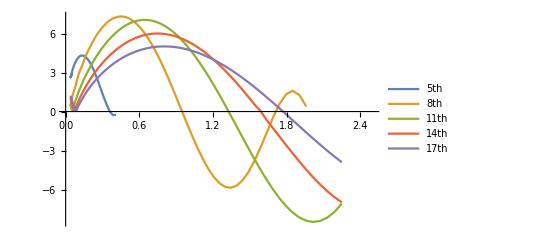

```mathematica
ListLinePlot[{
(If[#[[1]]<0.36,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[5]]),
(*(If[#[[1]]<0.6,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[6]]),*)
(*(If[#[[1]]<0.8||#[[1]]>1.7,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[7]]),*)
(If[#[[1]]<0.95||#[[1]]>1.7,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[8]]),
(*(If[#[[1]]<1.1||#[[1]]>1.7,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[9]]),*)
(*(If[#[[1]]<1.2||#[[1]]>1.7,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[10]])*)
(If[#[[1]]<1.3,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[11]]),
(If[#[[1]]<1.6,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[14]]),
(If[#[[1]]<1.75,RealAbs[#],{#[[1]],-RealAbs@#[[2]]}]&/@Aalltable[[17]])
},PlotLegends->(*{"5","6","7","8","9","10"}*)((ToString[#]<>"th")&/@{5,8,11,14,17}),PlotRange->{{0,2.5},Automatic}]
```

#### Debug

```mathematica
λ=10^-4;
```

```mathematica
H1[n_][ϕ_][x_?NumberQ]:=((m1^2-β^2)/x+(m2^2-β^2)/(1-x))ϕn[n][ϕ][x]; 
H2[n_][ϕ_][x_?NumberQ]:=2 β^2(ϕn[n][ϕ][x])/λ-β^2 NIntegrate[Boole[(y>x+λ||y<x-λ)](ϕn[n][ϕ][y])/(x-y)^2,{y,0,1},PrecisionGoal->15,Method->"AdaptiveMonteCarlo",MaxPoints->10^8,MaxRecursion->30];
```

```mathematica
(*H[n_][ϕ_][x_?NumberQ]:=NIntegrate[H1[n][x]-H2[n][x]+β^2(ϕ[n][x])/λ,{x,0,1}]*)
```

```mathematica
m1=0.5;m2=m1;
```

```mathematica
filename="/eigenstate_m-"<>ToString[m1]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Vals,ϕx}=Determineϕx[m1,m2,β,Nx];
Φ[x_]=ϕx;
Export[dir<>filename,{Vals,ϕx}]
},
{
{Vals,ϕx}=Import[dir<>filename];
Φ[x_]=ϕx;
}
];
```

```mathematica
Block[{x=1,y=1},Boole[(y>x+λ||y<x-λ)](ϕn[1][Φ][y])/(x-y)^2]
```

```mathematica
Plot3D[Boole[(y>x+λ||y<x-λ)](ϕn[1][Φ][y])/(x-y)^2,{y,0,1},{x,0,1}]
```

```mathematica
Plot[ϕn[10][Φ][x],{x,0,1}]
```

```mathematica
H2[1][Φ][0.3]
```

```mathematica
H1[1][Φ][0.3]
```

```mathematica
(Mn[1][Vals])^2 ϕn[1][Φ][0.3]
```

```mathematica
ListPlot[Table[{x,(Mn[#][Vals])^2 ϕn[#][Φ][x]-H1[#][Φ][x]-H2[#][Φ][x]&[1]},{x,0.1,0.9,0.1}]]
```

```mathematica
Kernel[x_?NumberQ]:=NIntegrate[Boole[(p>x+λ||p<x-λ)] ϕ3[p]/(p-x)^2,{p,0,1}]-(2ϕ3[x])/λ
```

```mathematica
{M2,ϕ2}={Mn[#][Vals],ϕn[#][Φ]}&[1];
{M3,ϕ3}={Mn[#][Vals],ϕn[#][Φ]}&[1];
{M1,ϕ1}={Mn[#][Vals],ϕn[#][Φ]}&[11];
```

```mathematica
ω[M1,M2,M3]
```

0.8852

```mathematica
({0,ω[M1,M2,M3]}-ω[M1,M2,M3])/(1-ω[M1,M2,M3])
```

{-7.71081,0.}

```mathematica
Kernel[-5]
```

1.62936250036972×10^659+1.01400639127469×10^672 ⅈ

```mathematica
Block[{ω=ω[M1,M2,M3]},NIntegrate[ϕ1[x]ϕ2[x/ω]Kernel[(x-ω)/(1-ω)],{p,0,1},{x,0,ω},AccuracyGoal->12,Method->"GlobalAdaptive"]]
```

$Aborted

```mathematica
Block[{ω=ω[M1,M2,M3]},NIntegrate[ϕ1[x]ϕ2[x/ω] ϕ3[p]/(p-(x-ω)/(1-ω))^2,{p,0,1},{x,λ,ω},AccuracyGoal->12,Method->"GlobalAdaptive"]]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.154651 and 0.0000366005 for the integral and error estimates.

{97.9281,-0.154651}

```mathematica
Block[{ω=ω[M1,M2,M3]},NIntegrate[ϕ1[x]ϕ2[x/ω] ϕ3[p]/(p-(x-ω)/(1-ω))^2,{p,0,1},{x,0,ω},AccuracyGoal->12,Method->"GlobalAdaptive"]]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.154651 and 0.000037968 for the integral and error estimates.

{94.5461,-0.154651}

```mathematica
Block[{ω=ω[M1,M2,M3]},NIntegrate[ϕ1[x]ϕ2[x/ω] ϕ3[p]/(p-(x-ω)/(1-ω))^2,{p,0,1},{x,0,ω},AccuracyGoal->12,Method->"LocalAdaptive"]]//AbsoluteTiming
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.885189}. NIntegrate obtained -0.0000134244 and 4.85595×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.885193}. NIntegrate obtained -0.0000257162 and 1.02403×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {3.22008×10^-6,0.885196}. NIntegrate obtained -0.0000662421 and 3.58037×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{83.0886,-0.154644}

```mathematica
A[ω_][ϕ1_,ϕ2_,ϕ3_]:=(1-ℂ)(1/(1-ω)NIntegrate[ϕ1[x]ϕ2[x/ω] ϕ3[p]/(p-(x-ω)/(1-ω))^2,{p,0,1},{x,0,ω},AccuracyGoal->12,Method->"GlobalAdaptive"]-1/ω NIntegrate[ϕ1[x]ϕ3[(x-ω)/(1-ω)] ϕ2[p]/(p-x/ω)^2,{p,0,1},{x,ω,1},AccuracyGoal->12,Method->"GlobalAdaptive"]+1/Nc 1/(1-ω)NIntegrate[ϕ3[x],{x,0,1}]NIntegrate[ϕ1[x]ϕ2[x/ω],{x,0,ω},AccuracyGoal->12,Method->"GlobalAdaptive"])(*r1=1*)
```

### NIntegration Test

#### Part1

```mathematica
NIntegrate[ϕ1[x]ϕ2[x/temp] ϕ3[p]/(p-(x-temp)/(1-temp))^2,{p,0,1},{x,0,temp}]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ2[x/temp]Kernel[(x-temp)/(1-temp)],{x,0,temp}]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ2[x/temp] ϕ3[p]/(p-(x-temp)/(1-temp))^2,{p,0,1},{x,0,temp},Method->"LocalAdaptive"]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ2[x/temp] ϕ3[p]/(p-(x-temp)/(1-temp))^2,{p,0,1},{x,0,temp},Method->"AdaptiveMonteCarlo",PrecisionGoal->20,MaxPoints->10^10]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ2[x/temp] ϕ3[p]/(p-(x-temp)/(1-temp))^2,{p,0,1},{x,0,temp},Method->"MultiPeriodic",PrecisionGoal->20]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ2[x/temp] ϕ3[p]/(p-(x-temp)/(1-temp))^2,{p,0,1},{x,0,temp},Method->"MonteCarloRule",PrecisionGoal->20,MaxPoints->10^9]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ2[x/temp] ϕ3[p]/(p-(x-temp)/(1-temp))^2,{p,0,1},{x,0,temp},Method->"NewtonCotesRule"]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ2[x/temp] ϕ3[p]/(p-(x-temp)/(1-temp))^2,{p,0,1},{x,0,temp},Method->"GaussBerntsenEspelidRule"]//AbsoluteTiming.
```

#### Part2

```mathematica
NIntegrate[ϕ1[x]ϕ3[(x-temp)/(1-temp)] ϕ2[p]/(p-x/temp)^2,{p,0,1},{x,temp,1}]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ3[(x-temp)/(1-temp)] ϕ2[p]/(p-x/temp)^2,{p,0,1},{x,temp,1},Method->"QuasiMonteCarlo",PrecisionGoal->20]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ3[(x-temp)/(1-temp)] ϕ2[p]/(p-x/temp)^2,{p,0,1},{x,temp,1},Method->"AdaptiveQuasiMonteCarlo"]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ3[(x-temp)/(1-temp)] ϕ2[p]/(p-x/temp)^2,{p,0,1},{x,temp,1},Method->"MonteCarlo",PrecisionGoal->20]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ3[(x-temp)/(1-temp)] ϕ2[p]/(p-x/temp)^2,{p,0,1},{x,temp,1},Method->"AdaptiveMonteCarlo",AccuracyGoal->20]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ3[(x-temp)/(1-temp)] ϕ2[p]/(p-x/temp)^2,{p,0,1},{x,temp,1},Method->"AdaptiveMonteCarlo",PrecisionGoal->20,MaxPoints->10^10]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ3[(x-temp)/(1-temp)] ϕ2[p]/(p-x/temp)^2,{p,0,1},{x,temp,1},Method->"LocalAdaptive"]//AbsoluteTiming
```

```mathematica
NIntegrate[ϕ1[x]ϕ3[(x-temp)/(1-temp)] ϕ2[p]/(p-x/temp)^2,{p,0,1},{x,temp,1},Method->"MultidimensionalRule"]//AbsoluteTiming
```

```mathematica
Plot3D[ϕ1[x]ϕ3[(x-temp)/(1-temp)] ϕ2[p]/(p-x/temp)^2,{x,temp,1},{p,0,1},PlotPoints->10,MaxRecursion->0]
```

```mathematica
ϕ1[x]ϕ3[(x-temp)/(1-temp)] ϕ2[p]/(p-x/temp)^2/.{x->0.95,p->0.5}
```

#### Part3

```mathematica
1/Nc NIntegrate[ϕ3[x],{x,0,1}]NIntegrate[ϕ1[x]ϕ2[x/temp],{x,0,temp}]//AbsoluteTiming
```

```mathematica
1/Nc NIntegrate[ϕ3[x],{x,0,1}]NIntegrate[ϕ1[x]ϕ2[x/temp],{x,0,temp},Method->"AdaptiveMonteCarlo",PrecisionGoal->20,MaxPoints->10^9]//AbsoluteTiming
```

```mathematica
1/Nc NIntegrate[ϕ3[x],{x,0,1}]NIntegrate[ϕ1[x]ϕ2[x/temp],{x,0,temp},Method->"LocalAdaptive"]//AbsoluteTiming
```

#### Sum

```mathematica
1/(1-temp)%%%[[2]]-1/temp%%[[2]]+1/Nc 1/(1-temp)%[[2]]
```

```mathematica
1/(1-temp)%%%[[2]]-1/temp%%[[2]]
```